```mathematica
SetOptions[ArrayPlot, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→All,DataReversed→False,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→False,MeshStyle→GrayLevel[-1+GoldenRatio],Method→Automatic,MissingStyle→Automatic,PixelConstrained→False,PlotLabel→None,PlotLayout→Automatic,PlotLegends→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

### Searching Larger Spaces for Specific Lifetime rules

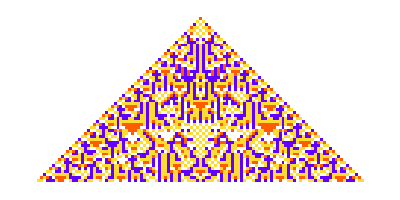
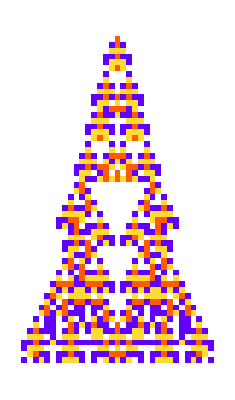
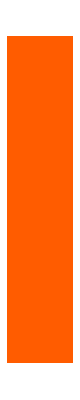
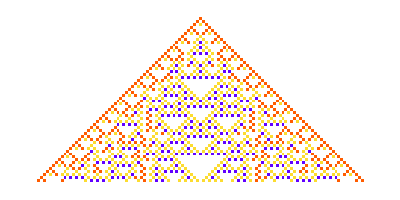
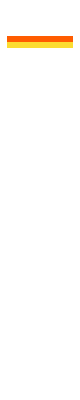
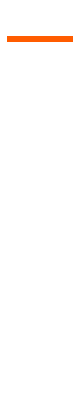
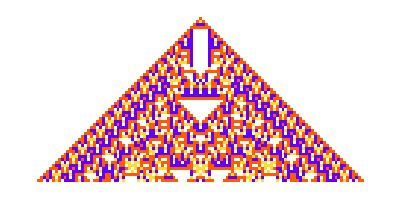
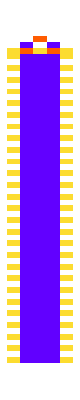
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, {{1}, 0}, 55], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"]], 10]
```

```mathematica
Table[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, {{1}, 0}, 55], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"]], 10]
```

```mathematica
rus = Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], 10000];
```

```mathematica
ByteCount[rus]
```

4480080

```mathematica
srus = ParallelTable[SeedRandom[112122+i]; ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], {i, 100000}];
```

```mathematica
vrus = ParallelSelect[srus,20<={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#, {{1}, 0}, 90]]<=80&];
```

```mathematica
Length[vrus]
```

40

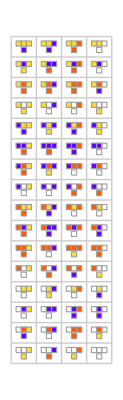

```mathematica
RulePlot[CellularAutomaton[{ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"]["RuleNumber"], 4, 1}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

```mathematica
vrus
```

{<|RuleNumber→32561875743987241466841889619665489436,Colors→4|>,<|RuleNumber→229898708168765926279069896212519287304,Colors→4|>,<|RuleNumber→260807496159467707741675661114091871760,Colors→4|>,<|RuleNumber→58715640301129914048925978275890797196,Colors→4|>,<|RuleNumber→64436472536250632761684513096706280248,Colors→4|>,<|RuleNumber→35305560154207811357607065018856678280,Colors→4|>,<|RuleNumber→215248966322771259804060638672785458064,Colors→4|>,<|RuleNumber→240512512478176989710280054420738978568,Colors→4|>,<|RuleNumber→183357174797289053283815121668568550792,Colors→4|>,<|RuleNumber→112573681466651911929040609961001995320,Colors→4|>,<|RuleNumber→217051397822232841968253387984304345992,Colors→4|>,<|RuleNumber→204741497224062537593819533583106100040,Colors→4|>,<|RuleNumber→54917752935031289732088675357240888588,Colors→4|>,<|RuleNumber→165507632831450002532572574358832417032,Colors→4|>,<|RuleNumber→199213115683655280381885264851321631036,Colors→4|>,<|RuleNumber→11292283855609075436122020013387029516,Colors→4|>,<|RuleNumber→216483149271834550672687724824239724872,Colors→4|>,<|RuleNumber→250239906986023996812133135372837842972,Colors→4|>,<|RuleNumber→258666315997938087524383308295844704712,Colors→4|>,<|RuleNumber→9536037450449423396530870716777405832,Colors→4|>,<|RuleNumber→51604906229548867864239784480625824060,Colors→4|>,<|RuleNumber→273687037089997078053796214631259180360,Colors→4|>,<|RuleNumber→242961881846224337442175649584293439800,Colors→4|>,<|RuleNumber→257734359961777134297902322408786719036,Colors→4|>,<|RuleNumber→5318335081886613398185464059355960460,Colors→4|>,<|RuleNumber→215330569904760740525167385729666258952,Colors→4|>,<|RuleNumber→330930584462622492373568757262747521936,Colors→4|>,<|RuleNumber→76681018509290293731851707053546701696,Colors→4|>,<|RuleNumber→150932988026146406594643943714638050876,Colors→4|>,<|RuleNumber→178189624054779666548105464542017326736,Colors→4|>,<|RuleNumber→41547670572156828211544627773115836732,Colors→4|>,<|RuleNumber→6173204659551047583514394799509057608,Colors→4|>,<|RuleNumber→203915437149468288645540752911870249288,Colors→4|>,<|RuleNumber→210993389785226489057778169498985059024,Colors→4|>,<|RuleNumber→110764579110370804416317914491321762188,Colors→4|>,<|RuleNumber→207745482524939076903487363673317235080,Colors→4|>,<|RuleNumber→20947733977656220124735877870525741964,Colors→4|>,<|RuleNumber→133677146492439797398158368974688756280,Colors→4|>,<|RuleNumber→167598306847262920712596649821997793848,Colors→4|>,<|RuleNumber→165924596695884140425766850573452753976,Colors→4|>}

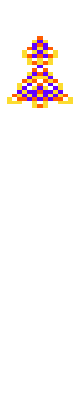
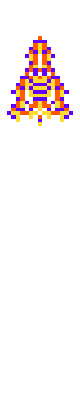
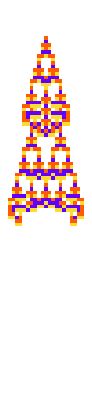
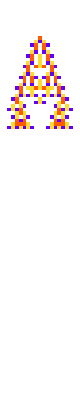
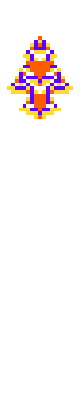
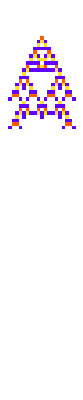
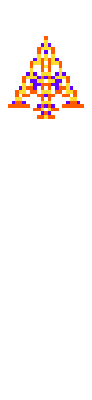
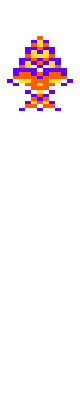

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, {{1}, 0}, 90], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ vrus
```

```mathematica
{{"[◼]", "TestCALifeTime"}}[CellularAutomaton[{#RuleNumber, 4, 1}, {{1}, 0}, 90]]&/@ vrus
```

{20,25,53,26,23,26,23,21,27,55,25,20,22,32,33,29,32,32,47,40,35,22,25,20,23,20,20,38,29,22,24,27,21,37,20,51,47,30,64,21}

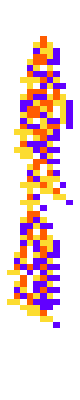
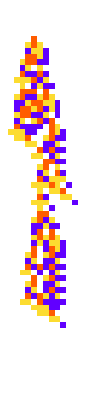
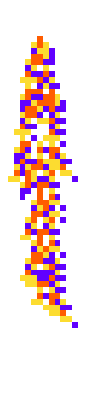
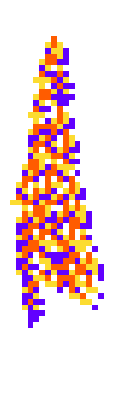
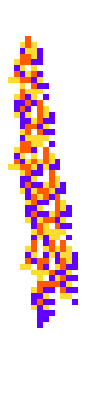
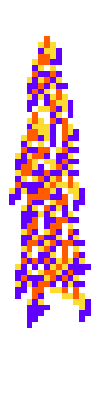
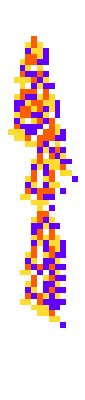
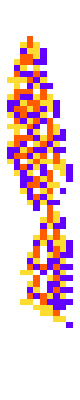
{-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50}

```mathematica
With[{ca = CellularAutomaton[#, {{1}, 0}, 55]}, Labeled[ArrayPlot[ca, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{{"[◼]", "TestCALifeTime"}}[ca]]]&/@
```

```mathematica
Iconize[{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1}}]
```

```mathematica
unique = ;
```

```mathematica
ResourceFunction["InteractiveListSelector"][CellularAutomaton[#, {{1}, 0}, 60]&/@ unique]
```

```mathematica
Iconize[{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1}}]
```

```mathematica
40^2
```

1600

```mathematica
Length[unique]
```

48

```mathematica
48^2
```

2304

```mathematica
Abs[{{1, 2}, {0, 3}} - {{2, 2}, {0, 3}}]
```

{{1,0},{0,0}}

```mathematica
mat = Table[Abs[Subtract@@(CellularAutomaton[#, {{1}, 0}, {52, {-20, 20}}]&/@ {unique[[i]] , unique[[j]]})], {i, 1, Length[unique]}, {j, i, Length[unique]}];
```

```mathematica
Map[Total, mat, {2}]
```

```mathematica
Map[Total[#, 2]&,, {2}]
```

{{0,481,432,619,621,583,472,516,517,373,661,654,777,697,587,607,607,605,705,554,463,355,501,494,480,493,519,632,632,508,451,367,431,557,554,471,736,519,398,454,552,571,597,539,464,595,619,506},{0,429,654,510,562,103,359,360,464,496,493,686,642,454,386,468,466,544,355,206,534,512,661,517,418,284,543,519,653,514,506,200,434,447,574,683,386,437,541,435,518,454,474,413,452,540,611},{0,629,505,603,410,430,431,411,579,576,763,689,483,523,539,537,673,472,417,447,445,596,478,467,401,540,590,616,435,461,391,515,516,539,570,479,382,520,486,507,545,441,440,543,573,528},{0,660,564,649,647,648,620,678,679,734,650,650,676,648,646,710,657,628,614,606,645,611,644,648,655,719,689,594,562,648,682,669,626,787,664,645,659,603,636,628,664,649,626,568,599},{0,644,505,457,456,580,556,553,762,726,500,468,454,452,478,433,494,704,542,785,633,466,476,83,509,767,614,590,468,458,465,734,747,528,551,595,549,458,454,546,525,452,626,735},{0,571,543,544,584,640,639,726,662,640,634,630,628,698,607,606,582,594,611,601,552,574,619,629,605,580,492,570,604,591,560,779,634,553,605,519,594,620,624,533,618,556,563},{0,320,321,473,503,500,693,649,443,367,473,471,573,378,185,545,507,642,506,425,257,538,512,660,491,483,177,437,450,569,664,357,428,528,428,511,459,461,408,457,545,602},{0,1,505,475,472,677,643,395,377,429,427,553,350,405,591,519,672,546,409,177,476,412,666,521,481,351,403,404,599,654,465,462,550,432,495,427,421,386,425,553,640},{0,506,476,473,678,644,396,378,430,428,554,351,406,592,520,673,547,410,178,475,411,667,522,482,352,404,405,600,653,466,463,551,433,496,428,420,387,426,554,641},{0,610,605,776,714,552,550,576,574,676,537,464,440,490,545,479,490,504,603,571,555,412,436,432,536,537,498,707,518,371,489,489,530,570,530,495,568,602,483},{0,13,290,198,618,450,434,432,522,435,548,618,592,681,631,576,454,539,525,727,618,598,520,522,503,508,757,662,569,711,559,590,440,624,527,438,384,679},{0,297,205,615,447,431,429,519,432,545,611,593,680,636,573,451,536,520,728,621,591,517,519,500,507,754,659,566,708,556,587,437,617,524,435,391,676},{0,268,814,664,652,650,742,655,750,698,742,675,777,768,664,745,761,775,720,758,708,736,717,636,945,824,755,817,721,780,658,824,711,656,568,669},{0,752,620,622,620,710,621,694,616,646,647,697,698,622,709,671,727,672,696,666,696,677,514,837,756,675,761,655,700,628,740,637,626,408,673},{0,520,514,514,546,439,432,658,576,761,571,494,332,519,585,743,568,548,448,514,515,678,691,390,515,581,549,498,512,412,447,512,620,691},{0,436,434,526,363,480,680,556,735,639,494,318,487,461,745,622,574,460,438,449,678,689,532,527,639,491,522,422,556,477,420,582,643},{0,2,434,315,508,660,542,713,633,496,420,427,489,759,582,536,492,436,423,670,749,584,553,637,529,474,88,564,409,90,534,711},{0,434,313,506,658,540,711,631,494,418,425,487,757,580,534,490,436,423,668,751,584,551,635,527,472,90,564,407,88,532,709},{0,505,564,762,666,783,703,566,526,435,579,783,684,652,570,508,493,742,863,618,651,675,647,530,436,612,575,436,616,785},{0,451,619,497,686,598,479,311,462,470,730,571,507,421,419,422,611,710,535,482,568,482,501,303,535,414,301,545,658},{0,540,518,667,479,434,400,527,565,669,462,450,154,426,439,610,687,332,419,497,475,514,494,430,427,492,596,629},{0,502,453,501,564,562,699,703,301,456,440,518,622,611,398,749,626,411,507,599,644,646,596,541,644,594,517},{0,643,509,462,526,585,567,639,514,470,482,604,599,554,675,530,413,595,505,534,538,584,495,536,522,575},{0,586,679,675,772,740,568,501,549,627,655,644,475,838,719,600,588,704,753,699,655,628,697,641,542},{0,469,541,644,614,566,495,471,493,553,546,523,704,513,466,520,496,565,605,531,506,603,557,572},{0,414,477,509,621,508,460,390,494,487,574,689,514,403,575,471,400,480,492,455,478,570,627},{0,495,493,677,516,480,384,422,423,576,677,476,481,569,437,490,418,408,389,416,534,633},{0,576,762,609,577,501,459,436,735,782,561,566,620,568,439,419,567,514,417,591,734},{0,750,645,575,535,511,518,681,670,615,544,642,518,553,473,585,542,471,585,716},{0,573,579,659,647,636,501,800,687,576,542,652,705,745,665,652,743,697,582},{0,404,438,588,577,486,749,534,427,553,533,572,568,550,545,566,546,469},{0,442,542,531,530,671,496,387,499,509,548,522,528,425,520,566,525},{0,422,435,590,681,338,403,511,463,502,478,404,397,476,564,591},{0,35,620,741,530,525,553,517,506,452,518,461,452,586,629},{0,609,742,543,510,566,522,509,441,519,450,441,571,618},{0,797,664,531,553,577,662,656,650,585,654,486,475},{0,695,638,756,666,753,747,657,700,749,717,778},{0,467,523,503,502,570,480,477,570,626,643},{0,526,480,479,547,535,472,545,545,514},{0,568,605,637,577,550,635,675,588},{0,495,515,541,488,513,461,598},{0,476,538,521,474,590,667},{0,560,413,2,532,697},{0,463,560,632,671},{0,411,527,598},{0,530,695},{0,577},{0}}

Phenotypic distance of

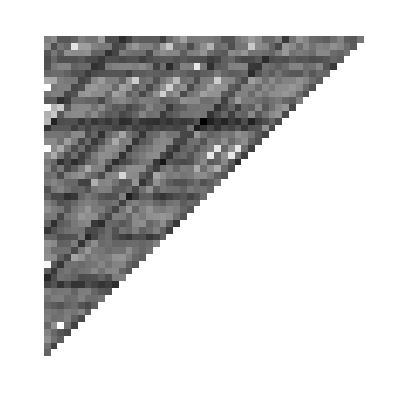

```mathematica
ArrayPlot[]
```

```mathematica
Total/@
```

{25526,21897,23121,28484,23578,25314,19396,18846,18876,20514,19492,19413,25003,22689,17893,17075,15459,15415,17965,14288,13332,14404,13656,15535,12553,11088,10394,11433,11129,11641,9105,8241,7255,7125,7041,7290,7856,5361,4643,4835,3611,3266,2204,2326,1536,1225,577,0}

```mathematica
Catenate@PositionLargest[, 10]
```

{4,1,6,13,5,3,14,2,10,11}

```mathematica
unique[[]]
```

{{319798423552890305951049955538759349516,4,1},{319777654365456166631348490314411963660,4,1},{319798423552890305951085984336315180300,4,1},{319839961927758584571537767554645521676,4,1},{319798428623492706863967561525572171020,4,1},{319777654365456169001755103751192737036,4,1},{320172208079476002584752447477961749772,4,1},{319777654365456166640571862351266739468,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1}}

### Running expansion algorithm

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
ClearAll@exhaustiveneutral
exhaustiveneutral[ru_, cut_:200]:= 
With[{lt = {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, cut]]}, Select[getallmutations[ru], {{"[◼]", "TestLifetime"}}[#, cut] == lt&]]
```

```mathematica
g = NestGraph[exhaustiveneutral[#, 55]&, , 2];
```

```mathematica
DeleteDuplicatesBy[Join[unique, VertexList[g]], CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1}}

```mathematica
Length[]
```

50

```mathematica
u2 = Join[unique, Union[]];
```

```mathematica
Length[u2]
```

83

```mathematica
Length@Union[u2]
```

50

```mathematica
Module[{mat = Table[Abs[Subtract@@(CellularAutomaton[#, {{1}, 0}, {52, {-20, 20}}]&/@ {u2[[i]] , u2[[j]]})], {i, 1, Length[u2]}, {j, i, Length[u2]}]},
tots = Total/@Map[Total[#, 2]&, mat, {2}];
next = Catenate[PositionLargest[tots, 10]];
u2[[next]]
]
```

{{319798423552890305951049955538759349516,4,1},{319839961927758584571537767554645521676,4,1},{319798423552890305951085984336315180300,4,1},{320172208079476002584752447477961749772,4,1},{319777654365456166631348490314411963660,4,1},{319798428623492706863967561525572171020,4,1},{319777654365456169001755103751192737036,4,1},{319175347929866126634869691242391565580,4,1},{319777654365456166640571862351266739468,4,1},{319819192739086505222314726046732940556,4,1}}

```mathematica
DeleteDuplicatesBy[Join[u2, VertexList[NestGraph[exhaustiveneutral[#, 55]&, u2[[next]], 2]]], CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1}}

```mathematica
u3 = ;
```

```mathematica
Length[DeleteDuplicatesBy[u2, CellularAutomaton[#, {{1}, 0}, 55]&]]
```

50

```mathematica
DeleteDuplicatesBy[Join[u3, VertexList[NestGraph[exhaustiveneutral[#, 55]&, u3, 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1}}

```mathematica
Length[]
```

90

```mathematica
ArrayPlot[CellularAutomaton[#, {{1}, 0}, 55], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DeleteDuplicatesBy[Join[, VertexList[NestGraph[exhaustiveneutral[#, 55]&, , 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1},{149698778482145237775049525580593394956,4,1},{319777654365456159252650860795694707980,4,1},{319777654365456176075504995300862113036,4,1},{319798427672754775582297470678644619020,4,1},{319798428623492743757491737741694399756,4,1},{319798428623492745823527073997164180748,4,1},{319819192739086504041705091480567969036,4,1},{319819192740324295400251251642673689868,4,1},{149698393101507336805294764326927496460,4,1},{319839576561976568536982068180250555660,4,1},{319839576561976569717573688760222905612,4,1},{319839637410442866184676200926524273932,4,1},{321168865406227782057580007986805142796,4,1},{319839799668482359821912845622658757900,4,1},{319839799689604107279057637669404947724,4,1},{319839961927758586924076345243586049292,4,1},{319839961927759037919566799770531689740,4,1},{319839961927759207924777634526315443468,4,1},{319839961927762815812771109885145019660,4,1},{319839961928996524611402985456934909196,4,1},{319839961928996524611402976385963980044,4,1},{320172267975966872813324633936476534028,4,1},{320172267975966872813324635035990258956,4,1},{320172268015580954070456802733250606348,4,1},{320338421475439987297437609819013674252,4,1},{329456034862536279106931457784252495116,4,1},{324159892066830773815299660706749379852,4,1}}

```mathematica
DeleteDuplicatesBy[Join[, VertexList[NestGraph[exhaustiveneutral[#, 55]&, , 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1},{149698778482145237775049525580593394956,4,1},{319777654365456159252650860795694707980,4,1},{319777654365456176075504995300862113036,4,1},{319798427672754775582297470678644619020,4,1},{319798428623492743757491737741694399756,4,1},{319798428623492745823527073997164180748,4,1},{319819192739086504041705091480567969036,4,1},{319819192740324295400251251642673689868,4,1},{149698393101507336805294764326927496460,4,1},{319839576561976568536982068180250555660,4,1},{319839576561976569717573688760222905612,4,1},{319839637410442866184676200926524273932,4,1},{321168865406227782057580007986805142796,4,1},{319839799668482359821912845622658757900,4,1},{319839799689604107279057637669404947724,4,1},{319839961927758586924076345243586049292,4,1},{319839961927759037919566799770531689740,4,1},{319839961927759207924777634526315443468,4,1},{319839961927762815812771109885145019660,4,1},{319839961928996524611402985456934909196,4,1},{319839961928996524611402976385963980044,4,1},{320172267975966872813324633936476534028,4,1},{320172267975966872813324635035990258956,4,1},{320172268015580954070456802733250606348,4,1},{320338421475439987297437609819013674252,4,1},{329456034862536279106931457784252495116,4,1},{324159892066830773815299660706749379852,4,1},{149698392784594686748237413952751695116,4,1},{149657240107276959154021281609959634188,4,1},{149698778482145237775049525855471301900,4,1},{319777634083046572423834571353610827020,4,1},{319777654365456176075504995300862080268,4,1},{319777654365456176089340053356144276748,4,1},{319798428623492743756338816237087552780,4,1},{319798428623493045988946641398988076300,4,1},{319798428623512088636640908063959479564,4,1},{319819192740324295105103346463320864012,4,1},{319839576561976569717573688760222906636,4,1},{319839799689604107279057637669404423436,4,1},{319839961927758584562893103808763442444,4,1},{319839961927758585743484724526174745868,4,1},{319839961927758586924040316446567085324,4,1},{319839961927759037919566799839251166476,4,1},{320006115427232322408890610408850486540,4,1},{319839961927762815812771110160022926604,4,1},{319839901081767713656391704544210121996,4,1},{319839961928996524610826515633660556556,4,1},{319839961928996524611402976385963455756,4,1},{320172267977204812852610014211375658252,4,1},{320172267975966872813324635310868165900,4,1},{320172207168352143115445530891496748300,4,1},{320338421476677927336722990093912798476,4,1},{321168865406227782057580011285340026124,4,1},{324159892066830773816452582211356226828,4,1},{329456034862536279102319771765825107212,4,1},{329456034862536279106787342596176639244,4,1}}

### Neutral search function

```mathematica
Nest[DeleteDuplicatesBy[Join[#, VertexList[NestGraph[exhaustiveneutral[#, 55]&, #, 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]&, , 1]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1},{149698778482145237775049525580593394956,4,1},{319777654365456159252650860795694707980,4,1},{319777654365456176075504995300862113036,4,1},{319798427672754775582297470678644619020,4,1},{319798428623492743757491737741694399756,4,1},{319798428623492745823527073997164180748,4,1},{319819192739086504041705091480567969036,4,1},{319819192740324295400251251642673689868,4,1},{149698393101507336805294764326927496460,4,1},{319839576561976568536982068180250555660,4,1},{319839576561976569717573688760222905612,4,1},{319839637410442866184676200926524273932,4,1},{321168865406227782057580007986805142796,4,1},{319839799668482359821912845622658757900,4,1},{319839799689604107279057637669404947724,4,1},{319839961927758586924076345243586049292,4,1},{319839961927759037919566799770531689740,4,1},{319839961927759207924777634526315443468,4,1},{319839961927762815812771109885145019660,4,1},{319839961928996524611402985456934909196,4,1},{319839961928996524611402976385963980044,4,1},{320172267975966872813324633936476534028,4,1},{320172267975966872813324635035990258956,4,1},{320172268015580954070456802733250606348,4,1},{320338421475439987297437609819013674252,4,1},{329456034862536279106931457784252495116,4,1},{324159892066830773815299660706749379852,4,1},{149698392784594686748237413952751695116,4,1},{149657240107276959154021281609959634188,4,1},{149698778482145237775049525855471301900,4,1},{319777634083046572423834571353610827020,4,1},{319777654365456176075504995300862080268,4,1},{319777654365456176089340053356144276748,4,1},{319798428623492743756338816237087552780,4,1},{319798428623493045988946641398988076300,4,1},{319798428623512088636640908063959479564,4,1},{319819192740324295105103346463320864012,4,1},{319839576561976569717573688760222906636,4,1},{319839799689604107279057637669404423436,4,1},{319839961927758584562893103808763442444,4,1},{319839961927758585743484724526174745868,4,1},{319839961927758586924040316446567085324,4,1},{319839961927759037919566799839251166476,4,1},{320006115427232322408890610408850486540,4,1},{319839961927762815812771110160022926604,4,1},{319839901081767713656391704544210121996,4,1},{319839961928996524610826515633660556556,4,1},{319839961928996524611402976385963455756,4,1},{320172267977204812852610014211375658252,4,1},{320172267975966872813324635310868165900,4,1},{320172207168352143115445530891496748300,4,1},{320338421476677927336722990093912798476,4,1},{321168865406227782057580011285340026124,4,1},{324159892066830773816452582211356226828,4,1},{329456034862536279102319771765825107212,4,1},{329456034862536279106787342596176639244,4,1},{149657240107276959154021281575599895820,4,1},{319819192755179575576527909762110354700,4,1},{319839799689603805047602734012110746892,4,1},{319839799689604031721193911755081004300,4,1},{335790535639023097753903322392768558348,4,1},{319839819952129299049710008755204977932,4,1},{319839901081767713656391704492670514444,4,1},{319839961926520644523607723533864318220,4,1},{319839941645348982091814300578923459852,4,1},{319756885179259967368770027692393035020,4,1},{319839961928996524610826515633660032268,4,1},{319839961928996524758400468223336969484,4,1},{320006115427232322408602380032698774796,4,1},{320006115427232323589482231126261789964,4,1},{320006115427232324770073851843673093388,4,1},{320338422426178551377116562173920572684,4,1},{320172267975966872813324635310866068748,4,1},{320172267977204812853474705339830793484,4,1},{320338421476658584523609156027117499660,4,1},{320338421476677927341334676112340186380,4,1},{324159892066830764371719616472065799436,4,1},{329456034862536279102320897665731949836,4,1},{244385443132301663240943690738234586380,4,1}}

```mathematica
Length[]
```

169

### More lenient neutral search function

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
ClearAll@exhaustiveneutral
exhaustiveneutral[ru_, cut_:200, range_:0]:= 
Module[{ca =CellularAutomaton[ru, {{1}, 0}, cut], lt}, 
lt = {{"[◼]", "TestCALifeTime"}}[ca]; Select[getallmutations[ru],lt-range<= {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, cut]] <= lt+range&]]
```

```mathematica
Nest[DeleteDuplicatesBy[Join[#, VertexList[NestGraph[exhaustiveneutral[#, 55, 2]&, #, 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]&, , 1]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1},{149698778482145237775049525580593394956,4,1},{319777654365456159252650860795694707980,4,1},{319777654365456176075504995300862113036,4,1},{319798427672754775582297470678644619020,4,1},{319798428623492743757491737741694399756,4,1},{319798428623492745823527073997164180748,4,1},{319819192739086504041705091480567969036,4,1},{319819192740324295400251251642673689868,4,1},{149698393101507336805294764326927496460,4,1},{319839576561976568536982068180250555660,4,1},{319839576561976569717573688760222905612,4,1},{319839637410442866184676200926524273932,4,1},{321168865406227782057580007986805142796,4,1},{319839799668482359821912845622658757900,4,1},{319839799689604107279057637669404947724,4,1},{319839961927758586924076345243586049292,4,1},{319839961927759037919566799770531689740,4,1},{319839961927759207924777634526315443468,4,1},{319839961927762815812771109885145019660,4,1},{319839961928996524611402985456934909196,4,1},{319839961928996524611402976385963980044,4,1},{320172267975966872813324633936476534028,4,1},{320172267975966872813324635035990258956,4,1},{320172268015580954070456802733250606348,4,1},{320338421475439987297437609819013674252,4,1},{329456034862536279106931457784252495116,4,1},{324159892066830773815299660706749379852,4,1},{149698392784594686748237413952751695116,4,1},{149657240107276959154021281609959634188,4,1},{149698778482145237775049525855471301900,4,1},{319777634083046572423834571353610827020,4,1},{319777654365456176075504995300862080268,4,1},{319777654365456176089340053356144276748,4,1},{319798428623492743756338816237087552780,4,1},{319798428623493045988946641398988076300,4,1},{319798428623512088636640908063959479564,4,1},{319819192740324295105103346463320864012,4,1},{319839576561976569717573688760222906636,4,1},{319839799689604107279057637669404423436,4,1},{319839961927758584562893103808763442444,4,1},{319839961927758585743484724526174745868,4,1},{319839961927758586924040316446567085324,4,1},{319839961927759037919566799839251166476,4,1},{320006115427232322408890610408850486540,4,1},{319839961927762815812771110160022926604,4,1},{319839901081767713656391704544210121996,4,1},{319839961928996524610826515633660556556,4,1},{319839961928996524611402976385963455756,4,1},{320172267977204812852610014211375658252,4,1},{320172267975966872813324635310868165900,4,1},{320172207168352143115445530891496748300,4,1},{320338421476677927336722990093912798476,4,1},{321168865406227782057580011285340026124,4,1},{324159892066830773816452582211356226828,4,1},{329456034862536279102319771765825107212,4,1},{329456034862536279106787342596176639244,4,1},{149657240107276959154021281575599895820,4,1},{319819192755179575576527909762110354700,4,1},{319839799689603805047602734012110746892,4,1},{319839799689604031721193911755081004300,4,1},{335790535639023097753903322392768558348,4,1},{319839819952129299049710008755204977932,4,1},{319839901081767713656391704492670514444,4,1},{319839961926520644523607723533864318220,4,1},{319839941645348982091814300578923459852,4,1},{319756885179259967368770027692393035020,4,1},{319839961928996524610826515633660032268,4,1},{319839961928996524758400468223336969484,4,1},{320006115427232322408602380032698774796,4,1},{320006115427232323589482231126261789964,4,1},{320006115427232324770073851843673093388,4,1},{320338422426178551377116562173920572684,4,1},{320172267975966872813324635310866068748,4,1},{320172267977204812853474705339830793484,4,1},{320338421476658584523609156027117499660,4,1},{320338421476677927341334676112340186380,4,1},{324159892066830764371719616472065799436,4,1},{329456034862536279102320897665731949836,4,1},{244385443132301663240943690738234586380,4,1},{149657240107238273527793613442009298188,4,1},{149657240107276052459656570603718866188,4,1},{149657240107276959154021211206855718156,4,1},{149657245177879360066938887562412717324,4,1},{149657240107199587901565945342778438924,4,1},{149657240107276940264555350131378779404,4,1},{149657240107276959153444820857656210700,4,1},{149698453948736147760306036168681354508,4,1},{149698777516552007132452911159276500236,4,1},{149698778467289957303624962264624035084,4,1},{149698778467289957303624962281837458700,4,1},{149698778467289957303624997466175993100,4,1},{149698778467289957524985891166318523660,4,1},{149698778482145256664515457059174249740,4,1},{153686462469499985393760946761434428684,4,1},{149698778482145237922623478445147714828,4,1},{234769370198761908736332514318307063052,4,1},{234769370198761908740944270705478628620,4,1},{236098598194546824609236391747331585292,4,1},{234769207939485081884152434543863559436,4,1},{234769370198761911097518077921687532812,4,1},{234769370198762213328970729779167524108,4,1},{244385443132301663240943690738234586636,4,1},{244385443132379034493399027005415781644,4,1},{319175287082637314499482971465340187916,4,1},{319175287082637315670851220145896715532,4,1},{319175292153239716592992198169564312844,4,1},{319175347929827422119176096028265837836,4,1},{319175347929827440123198311968789001484,4,1},{319175347929827440713494122327494653196,4,1},{319175347929827441008644279306661164300,4,1},{319839961927758584571321594772531737868,4,1},{319839961927758584718895547362208150796,4,1},{319175347949692510081161295726000239884,4,1},{149615701718790735637082723976508929292,4,1},{319756885179259967368770027640853427468,4,1},{319756885179259967368770027692393033996,4,1},{319777654365451329747478551817790190860,4,1},{319777654365451367526410274037463545100,4,1},{319777654365456159252650860795694691596,4,1},{319777654365456159252650860795963143436,4,1},{319777654365456159252650860796231578892,4,1},{319777654365460994955929319312393532684,4,1},{319777653414718209376626714852520129804,4,1},{319777654365456159547798765975047517452,4,1},{319777654365460995251077224491746358540,4,1},{319777654365451330928070031797176284428,4,1},{319777654365456166640571862350729884940,4,1},{319777654365456166631347927364458542348,4,1},{319777654365456169075542080046030943500,4,1},{319777654367932049080325864300990985484,4,1},{319777654365456176075432937706824152332,4,1},{319777654365456478306959898958155756812,4,1},{319777410976540932255459907933846680844,4,1},{319777654365451340372226536784163288332,4,1},{319777654365456176075504995300593677580,4,1},{319777654365456478306959898958155789580,4,1},{319777654365451340372802997536466711820,4,1},{319777654365456176076081456053165552908,4,1},{319777654365456176085304828090020312332,4,1},{319777654365456251647203779270467695884,4,1},{319777654365456478320794957013437953292,4,1},{319798261293608641033867673489302648076,4,1},{319798423552885469066639444349901632780,4,1},{319798423552885470247231065067312411916,4,1},{335749159502304460722076749790677071116,4,1},{319798423552890305951049955607478826252,4,1},{319798423552890305951085702861338469644,4,1},{319798423552890302483098098478651045132,4,1},{319798423552890307200852895329868870924,4,1},{319798423552890324845163601832786556172,4,1},{319798423552890334285284881553649595660,4,1},{319798423554128264879837296089258292492,4,1},{319798423551652365911224143309112636684,4,1},{319798423555366186029080284958443730188,4,1},{319798423555366186029080301725996053772,4,1},{319798423555366195473813249873100436748,4,1},{319798423555366790491990091448397362444,4,1},{319798427672754775581721009926341195532,4,1},{319798427989667425639354821052820420364,4,1},{319798428623454021237739893391981573388,4,1},{330432252589772033847198018007814927628,4,1},{319798428623492707749411277063630648588,4,1},{319798428623492708044559182242983458060,4,1},{319798428623454022639692442993907496204,4,1},{298530780690934071787008608836686476556,4,1},{319798428623487890050191063284473165068,4,1},{319798428623492725753469662538660345100,4,1},{319798428623492735198202487540462417164,4,1},{319798428623454040127241853667581424908,4,1},{319798428623492725752893061048868599564,4,1},{319798428623492743830125792531925759244,4,1},{319798428623493045987793719894381229324,4,1},{319798418482287941931656525768068756748,4,1},{319798428623454058131264069608103802124,4,1},{319798428623492743757491737741694387468,4,1},{319798428623492743757491737741711176972,4,1},{319798428623454059016707785146162279692,4,1},{319798428623502416049492370313150526732,4,1},{319798428623570117075982410264345376012,4,1},{319839966998361024444555317967797941516,4,1},{319777659436058906678432519413671195916,4,1},{319798428623493027099480709920407221516,4,1},{319798428623493045988928627000478594316,4,1},{319798428623493045988946641364628337932,4,1},{319839966998361324609974885369621837068,4,1},{319797779586404771783187341751918327052,4,1},{319819030479809676008951338866232309004,4,1},{319819030479809676156525287057862210828,4,1},{319819030479809677189542955185597101324,4,1},{319819030479809713787883197425347507468,4,1},{319819030479809978240406238125479474444,4,1},{319819030479809675713803429289369842956,4,1},{319819030479809676007798412964115821836,4,1},{319819030479809676008952460368629511436,4,1},{319819030483523496126807475293420041484,4,1},{319819187672197922066070019449794884876,4,1},{323806876092615953907503067746389488908,4,1},{319819192739086504041633033886530041100,4,1},{319819192739086504041705232218056324364,4,1},{319819192422173855165257375672557139212,4,1},{319819192739086505221738265294429517068,4,1},{319819192739086506402879325716135834892,4,1},{319819192739086506398294379820495959308,4,1},{319819192739087110865815873153510700300,4,1},{319819192739086506402909725013620585740,4,1},{319819192739086507583497968031311361292,4,1},{319819192739086544181838210271061767436,4,1},{319819192750227815419386388662513857804,4,1},{319819192742800327701354108581130827020,4,1},{319819192742800327848928060895929333004,4,1},{319819192755179575575374988257503507724,4,1},{319819192755189246983084826795508004108,4,1},{319839576576831697892679179512954254604,4,1},{319839575928151268422867367294459999500,4,1},{319839576561976568536982068042809505036,4,1},{319839576561976568536983193942718444812,4,1},{319839576561976606315913930999973311756,4,1},{319839576563214508576267448317710726412,4,1},{319839576561976568536928024984722109708,4,1},{319839576561976568536982068180248458508,4,1},{319839576561976568536982208917738910988,4,1},{319839576563214508576267448455149679884,4,1},{319839576561976569718150149512526329100,4,1},{319839576561976569865147641349899318540,4,1},{319839576563214509756859069035122029836,4,1},{319839576561976569717573687660711278860,4,1},{319839576561976569718150149512526330124,4,1},{319839576245064069595652169497282639116,4,1},{319839576561976719652709519871456343308,4,1},{319839576561986391059266436904856089868,4,1},{319839637410443470647586008241112151308,4,1},{319839638678093466412905602423228003596,4,1},{319839799034656908591242030714224145676,4,1},{319839799668482207524765110745164444940,4,1},{319839799668482208705356731462575781132,4,1},{319839799668487044408635189979274573068,4,1},{319839799669720148744642111737474872588,4,1},{319839799688289249333922815860961735948,4,1},{319756722918745802579856357681391236364,4,1},{319839799668482208706185393794011919628,4,1},{319839475149928701395222091263657145612,4,1},{319839799668443674195721206286087124236,4,1},{319839799668481453127584163447796692236,4,1},{319922876418218917064005362360945243404,4,1},{319839759124707528723261453507721180428,4,1},{319839799689526736026602301402223748364,4,1},{319839799689526740748968784271868966156,4,1},{319175185691711347111150830481970574604,4,1},{319839738842374994092591462170356888844,4,1},{319839799689603805046449812507503899916,4,1},{319839799689603805047602171062157325580,4,1},{319839799689603805047603859912017589516,4,1},{319839799689603814492335699751401174284,4,1},{319839799689613476454159651045508396300,4,1},{335790535639022795522448418735474881804,4,1},{319839150652496714867740345443039851788,4,1},{319839799669796991092627827356695016716,4,1},{319839799689604031725805597773508392204,4,1},{321169027685388947594097718815361348876,4,1},{319839799689604107274445951650977035532,4,1},{319839799689613778685614554702802072844,4,1},{319839799689604107278985580075367019788,4,1},{319839799689604107283669323687832335628,4,1},{319839799689604711741967444983992300812,4,1},{335790535639023097753903322392769082636,4,1},{319839819952051927797254672488023782668,4,1},{319839819952090613423482340621614380300,4,1},{319839819952206670302165345022386173196,4,1},{319839901080529772435934874995480360204,4,1},{319839901080529773616526495712891659532,4,1},{319777593518227959557598126712822723852,4,1},{319839252043423060635686926356732212492,4,1},{319839901081767712475800083826798818572,4,1},{319839901081767716017574945979032728844,4,1},{319839901082077198666213049612934903052,4,1},{319839941646586920959732552438712694028,4,1},{319839941645348977369447817709278246156,4,1},{319839941645348979730631059144100853004,4,1},{319839941645348982091814300544563721484,4,1},{319839941645348982091814309375016482060,4,1},{322498397636918813837621914699484149004,4,1},{323827625632703729710525721759764493580,4,1},{319839961926520663413073655012445173004,4,1},{319839961926520682302539586491026027788,4,1},{319839961926530315930164640567261967628,4,1},{319175347929866126626441200278623270156,4,1},{319839961927758584562893033440019264780,4,1},{319839961927758584784254032693278061836,4,1},{319839961947565625191459188207149430028,4,1},{319839963195409184791122505305466647820,4,1},{319839961927758584569015822132062221580,4,1},{319839961927758584571321383666299204876,4,1},{319839961926520644532252387279746397452,4,1},{319839961927758584571537767554643424524,4,1},{319839961927758660129401493468968940812,4,1},{319839960977020635572312673403647341836,4,1},{319839961927758586932576893801123837196,4,1},{319839961927758887984016637493846504716,4,1},{319839961927758888131590585685476406540,4,1},{298572313995199932957579403482081572108,4,1},{319839961293933286809925615698215482636,4,1},{319839961927758586924040034971590374668,4,1},{319839960977020636752904293983619691788,4,1},{319839960977020636752904294121058645260,4,1},{319839961927753751220797890987494257932,4,1},{319839961927758586924075786554239661324,4,1},{319839961927758586924076349504201471244,4,1},{319839961927758586924075223604286764300,4,1},{319839956857156186011159869417287628044,4,1},{321169189923543502796981282464380794124,4,1},{319839961927758582210933238671403152652,4,1},{298572313995199933031402412834546300172,4,1},{319839961927719901371635657665441215756,4,1},{319839961927758586997862199899124970764,4,1},{319839961927758735687265219383292359948,4,1},{319839961927759037918720123040585774348,4,1},{319839961927759037918720123040586020108,4,1},{319839961927836409171175459307767231756,4,1},{319777654365456619988024433814581048588,4,1},{319839312890651721066113233458490537228,4,1},{319839961927681666667111463503350494476,4,1},{319839961927759037034123084232473212172,4,1},{319839961927759037919494742176493761804,4,1},{319839961927836409172022136037712885004,4,1},{319839961942614318390991363069321180428,4,1},{319839961927759037919566799838982731020,4,1},{319839961927759037919566800663884887308,4,1},{319839961927759037919580310569413801228,4,1},{319839961927759037919584814169040909580,4,1},{319839964463060238376043617162447582476,4,1},{319839961927754353332033807480922076428,4,1},{319839961927759189035312265997618803980,4,1},{319923038677495746277368753938888422668,4,1},{319839961927759189035307762398060639500,4,1},{319839961927759207629629729346962617612,4,1},{319839961927762815812771127752208971020,4,1},{319839961928996222379944704924554392844,4,1},{319839961928919153358371179366478837004,4,1},{319839961928996524610826515633659983116,4,1},{319839961928996524610826515633659999500,4,1},{319839880799358110004144819844655412492,4,1},{319839961928996524610826515633660507404,4,1},{319839961928996524610826520031707067660,4,1},{319839961928996526972582847817647420684,4,1},{319839961928996543500865537861405668620,4,1},{319839961928996525791991229299259372812,4,1},{319839961928996543500865540060428924172,4,1},{319839961948803565239965692980234056972,4,1},{319839961927758584572117596111064331532,4,1},{319839961928996524611402976935719269644,4,1},{319839961295171224497288275637612377356,4,1},{319839961928996524611402976385427109132,4,1},{319839961928996524611402976935719793932,4,1},{319923038678733081853459464327231501580,4,1},{320006115428469639095515952268499023116,4,1},{234769370198761908745559332224603321612,4,1},{319839961928996524316255078903192548620,4,1},{319839961928996524611402984082545325324,4,1},{319839961928996524316255079178070455564,4,1},{319839961928996524611348941161894835468,4,1},{319839961928996524611402984357423232268,4,1},{319839961928996543500868915836004136204,4,1},{319839961928996524316255080002704176396,4,1},{319839961928996524611402985182056953100,4,1},{319839961928996543500868916660637857036,4,1},{319839961928996826842857888839350678796,4,1},{330473785895275851594633441664299758860,4,1},{319839961928996524316255080277582083340,4,1},{319839961928996524611402985456934860044,4,1},{319839961928996543500868916935515763980,4,1},{319923038678733081853459473398202430732,4,1},{319839961928996524316255081102215804172,4,1},{319839961928996524611186813499454846220,4,1},{319839961928996524611402986281568580876,4,1},{319839961928996524316255081377093711116,4,1},{319839961928996524611402986556446487820,4,1},{319839961928996543500868918035027391756,4,1},{319839961948803560517599210110588826892,4,1},{319839961948803565239965692980234041612,4,1},{319839961948803565239966818880140883212,4,1},{320006115448276679724078668862769083660,4,1},{320006115427232322408602380032707163404,4,1},{320006115427232322408603505932605617420,4,1},{320006115427232322408605757732419302668,4,1},{320006034297593907802208914619845342476,4,1},{320006115427232322413502296427277874444,4,1},{323993799414587070027602031589691520268,4,1},{256203171629556362870691112950216553740,4,1},{320006115427232324770073851843672831244,4,1},{320006115427232324770073851843673109772,4,1},{320006115427232324770073852393428907276,4,1},{320006115429708204848644612393471341836,4,1},{320006439945785983196800634999693669644,4,1},{323993799414587072388785273024514127116,4,1},{320172207168352143115445530891496731916,4,1},{320172207168352143115445530891496764684,4,1},{320172208079476002584752447426422142220,4,1},{320172208079476002584752447615400703244,4,1},{320172208079476021474218378956542604556,4,1},{320172267975966872813325759836383376652,4,1},{320172267975967175044779537593770210572,4,1},{235101676245732256947480982078536578316,4,1},{320172267975347902793681943799029069068,4,1},{320172267975966872804101261899623855372,4,1},{320109960413664454881782269080039617804,4,1},{320172266708316272585095233539287053580,4,1},{320172267975966872812171713531383411980,4,1},{320172267975966871632733014593454765324,4,1},{320172267975966872813324635276506330380,4,1},{320172267975966871632733014593456862476,4,1},{320172267975966872813324635276508427532,4,1},{320172267977204811967166298673317180684,4,1},{320172267977204812557462109032022832396,4,1},{320172267977204811968030989801772315916,4,1},{320172267977204812558326800160477967628,4,1},{320172257874376152244621590759624963340,4,1},{320172268015580954070456239783297185036,4,1},{320172268015580954070456802733250589964,4,1},{320172268015580954070456802733250622732,4,1},{320172268926704822984352569870930179340,4,1},{320338421475439987298590531323620521228,4,1},{320338421476658565634143224548536644876,4,1},{320338421476658584523609156027117500684,4,1},{150197238016208695605035686378028692748,4,1},{320317652289243788026208868108595918092,4,1},{320338421476677926746427179735207146764,4,1},{320338421476677927334417147084699104524,4,1},{320338421476677927410509966388751004940,4,1},{320338380911858720037993828217837614348,4,1},{320338421476677927340181754607733339404,4,1},{320338421476677927341335802012247029004,4,1},{320338421476677927341336927912153871628,4,1},{320338421476677927562695604996854805772,4,1},{320338424961479751833575365167326983436,4,1},{321168865406227781762432102807452316940,4,1},{321168865406227782052968321968377754892,4,1},{321168865406227781762432106105987200268,4,1},{322477263366112109856548108349408572684,4,1},{322498032553546248281618514796666975500,4,1},{324139122879357929989088561409540519180,4,1},{324139122879396615615316282319689250060,4,1},{324139122879396615615319607242851644684,4,1},{324139122879396616795907850260542420236,4,1},{324159892066830750203463859862709761292,4,1},{324159892066830750203463868796241736972,4,1},{324159891749918104868773001137092326668,4,1},{324159892066792069299602683377677530380,4,1},{324159892066830754916606979474413352204,4,1},{324159892066830754925830351648707081484,4,1},{324159892066830754925829788578494575884,4,1},{324159892066830754925830351528447210764,4,1},{324159892066830754925830351734606427404,4,1},{324159892066830755073404304118124410124,4,1},{324159892066830754040390013690110047500,4,1},{324159892066830754630685824048815699212,4,1},{324159892066830754925833729228168524044,4,1},{324159892066985497430744401762530915596,4,1},{323827585067884535403493664706995713292,4,1},{324159729807553935158356224894055511308,4,1},{324159892066830764371719615372554171660,4,1},{324159892066830764371719616454885930252,4,1},{324159892066830764371719617571577427212,4,1},{324159892066830764371719634064251843852,4,1},{324159892066830773816452581111844599052,4,1},{324159892066830773816452583310867854604,4,1},{324159892066830773816452652580100404492,4,1},{329476804049970437308067810452477605132,4,1},{334793716033110100799683038693598983436,4,1},{324159952914059565880841623370199758092,4,1},{329456034862536278512023961407119455500,4,1},{329456034862536279102319771765825139980,4,1},{329456034862536279102319771971983537420,4,1},{329456034862536278216877182127673472268,4,1},{329456034862536278807172992486379123980,4,1},{329456034862536279102302883267222467852,4,1},{329456034862536279323681826550246569228,4,1},{334772946845675942593936125906853328140,4,1},{329456034862536279106789594395990324492,4,1},{329456034862536278811783552604899669260,4,1},{329456034862536279106931457784251708684,4,1},{329456034862536279106931457784251970828,4,1},{335748997264154819132875078422134797580,4,1},{335790535639023097753904448292675400972,4,1}}

```mathematica
Length[]
```

573

```mathematica
ArrayPlot[CellularAutomaton[#, {{1}, 0}, 55], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@[[-10;;]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Nest[DeleteDuplicatesBy[Join[#, VertexList[NestGraph[exhaustiveneutral[#, 55, 2]&, #, 1]]], CellularAutomaton[#, {{1}, 0}, 55]&]&, , 1]
```

```mathematica
Length[]
```

72635

```mathematica
Iconize[]
```

```mathematica
lg = ;
```

```mathematica
SeedRandom[111111];
{{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#, {{1}, 0}, 55]]&/@ RandomSample[, 100]
```

{48,51,48,52,52,49,48,50,49,49,50,49,52,49,52,50,52,49,50,49,50,48,50,49,48,52,48,48,52,50,52,48,50,51,49,49,50,50,49,51,52,50,50,48,48,50,49,51,49,52,49,48,49,48,50,50,52,50,50,52,48,52,49,52,51,48,49,50,50,50,49,50,49,49,50,51,49,50,48,50,49,52,49,50,51,48,51,52,51,48,50,52,50,51,48,52,49,50,50,48}

```mathematica
ParallelSelect[lg, 48<={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#, {{1}, 0}, 55]]<=52&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1},{319798428623492708265920111127498093836,4,1},{324159892066830754925830351528447997196,4,1},{319175347929866126634869761611135743244,4,1},{319175347929866126782443643832067978508,4,1},{319175347929827441008642027506847479052,4,1},{319839961927758584571321665141275915532,4,1},{319175347929885469452595211327614252300,4,1},{234769370198761911097515826121873847564,4,1},{319175347929827441008642027506846692620,4,1},{319777654365456159547798765975047533836,4,1},{319777654365456176076081456053165536524,4,1},{319777659436058567544266096300687930636,4,1},{319798428623492725753469521801172023052,4,1},{319798428623492744642935453279752877324,4,1},{319819030479809676008951334468185797900,4,1},{319819192105261206288791646565548455180,4,1},{319819192739086506402888332915390575884,4,1},{319819192739086506402906065838923347212,4,1},{319819192740324295400251251505234736396,4,1},{319819187672197926788436502319440098572,4,1},{322498032553546249167062230334725453068,4,1},{319839576561976568536982068042811602188,4,1},{319839961927758586924076345106147095820,4,1},{319839961927758586924076349504193082636,4,1},{319839961927758586924077475404100449548,4,1},{319839961927758586997863325799031813388,4,1},{319839799668482208705356731462575748364,4,1},{319839961927759037919584814169041171724,4,1},{149698778467289957303624962281803904268,4,1},{319839799668482359821948874419677721868,4,1},{319839961927759189035311703047734588684,4,1},{319839961927759189035312265997620901132,4,1},{319839637410442866184676200926524798220,4,1},{319839961928996524611402984357423281420,4,1},{319839961928996524611402985182057002252,4,1},{319839961928996524611402986556446536972,4,1},{319839799689526736026602301402223752460,4,1},{320172267975966872813324633936478631180,4,1},{324139122879396615615316229543131116812,4,1},{324159892066830754925830351511268128012,4,1},{324159892066830754925833729228168525068,4,1},{324159952914059565880841623370201855244,4,1},{149698778482145237775049525580593394956,4,1},{319777654365456159252650860795694707980,4,1},{319777654365456176075504995300862113036,4,1},{319798427672754775582297470678644619020,4,1},{319798428623492743757491737741694399756,4,1},{319798428623492745823527073997164180748,4,1},{319819192739086504041705091480567969036,4,1},{319819192740324295400251251642673689868,4,1},{149698393101507336805294764326927496460,4,1},{319839576561976568536982068180250555660,4,1},{319839576561976569717573688760222905612,4,1},{319839637410442866184676200926524273932,4,1},{321168865406227782057580007986805142796,4,1},{319839799668482359821912845622658757900,4,1},{319839799689604107279057637669404947724,4,1},{319839961927758586924076345243586049292,4,1},{319839961927759037919566799770531689740,4,1},{319839961927759207924777634526315443468,4,1},{319839961927762815812771109885145019660,4,1},{319839961928996524611402985456934909196,4,1},{319839961928996524611402976385963980044,4,1},{320172267975966872813324633936476534028,4,1},{320172267975966872813324635035990258956,4,1},{320172268015580954070456802733250606348,4,1},{320338421475439987297437609819013674252,4,1},{329456034862536279106931457784252495116,4,1},{324159892066830773815299660706749379852,4,1},{149698392784594686748237413952751695116,4,1},{149657240107276959154021281609959634188,4,1},{149698778482145237775049525855471301900,4,1},{319777634083046572423834571353610827020,4,1},{319777654365456176075504995300862080268,4,1},{319777654365456176089340053356144276748,4,1},{319798428623492743756338816237087552780,4,1},{319798428623493045988946641398988076300,4,1},{319798428623512088636640908063959479564,4,1},{319819192740324295105103346463320864012,4,1},{319839576561976569717573688760222906636,4,1},{319839799689604107279057637669404423436,4,1},{319839961927758584562893103808763442444,4,1},{319839961927758585743484724526174745868,4,1},{319839961927758586924040316446567085324,4,1},{319839961927759037919566799839251166476,4,1},{320006115427232322408890610408850486540,4,1},{319839961927762815812771110160022926604,4,1},{319839901081767713656391704544210121996,4,1},{319839961928996524610826515633660556556,4,1},{319839961928996524611402976385963455756,4,1},{320172267977204812852610014211375658252,4,1},{320172267975966872813324635310868165900,4,1},{320172207168352143115445530891496748300,4,1},{320338421476677927336722990093912798476,4,1},{321168865406227782057580011285340026124,4,1},{324159892066830773816452582211356226828,4,1},{329456034862536279102319771765825107212,4,1},{329456034862536279106787342596176639244,4,1},{149657240107276959154021281575599895820,4,1},{319819192755179575576527909762110354700,4,1},{319839799689603805047602734012110746892,4,1},{319839799689604031721193911755081004300,4,1},{335790535639023097753903322392768558348,4,1},{319839819952129299049710008755204977932,4,1},{319839901081767713656391704492670514444,4,1},{319839961926520644523607723533864318220,4,1},{319839941645348982091814300578923459852,4,1},{319756885179259967368770027692393035020,4,1},{319839961928996524610826515633660032268,4,1},{319839961928996524758400468223336969484,4,1},{320006115427232322408602380032698774796,4,1},{320006115427232323589482231126261789964,4,1},{320006115427232324770073851843673093388,4,1},{320338422426178551377116562173920572684,4,1},{320172267975966872813324635310866068748,4,1},{320172267977204812853474705339830793484,4,1},{320338421476658584523609156027117499660,4,1},{320338421476677927341334676112340186380,4,1},{324159892066830764371719616472065799436,4,1},{329456034862536279102320897665731949836,4,1},{244385443132301663240943690738234586380,4,1},{149657240107238273527793613442009298188,4,1},{149657240107276052459656570603718866188,4,1},{149657240107276959154021211206855718156,4,1},{149657245177879360066938887562412717324,4,1},{149657240107199587901565945342778438924,4,1},{149657240107276940264555350131378779404,4,1},{149657240107276959153444820857656210700,4,1},{149698453948736147760306036168681354508,4,1},{149698777516552007132452911159276500236,4,1},{149698778467289957303624962264624035084,4,1},{149698778467289957303624962281837458700,4,1},{149698778467289957303624997466175993100,4,1},{149698778467289957524985891166318523660,4,1},{149698778482145256664515457059174249740,4,1},{153686462469499985393760946761434428684,4,1},{149698778482145237922623478445147714828,4,1},{234769370198761908736332514318307063052,4,1},{234769370198761908740944270705478628620,4,1},{236098598194546824609236391747331585292,4,1},{234769207939485081884152434543863559436,4,1},{234769370198761911097518077921687532812,4,1},{234769370198762213328970729779167524108,4,1},{244385443132301663240943690738234586636,4,1},{244385443132379034493399027005415781644,4,1},{319175287082637314499482971465340187916,4,1},{319175287082637315670851220145896715532,4,1},{319175292153239716592992198169564312844,4,1},{319175347929827422119176096028265837836,4,1},{319175347929827440123198311968789001484,4,1},{319175347929827440713494122327494653196,4,1},{319175347929827441008644279306661164300,4,1},{319839961927758584571321594772531737868,4,1},{319839961927758584718895547362208150796,4,1},{319175347949692510081161295726000239884,4,1},{149615701718790735637082723976508929292,4,1},{319756885179259967368770027640853427468,4,1},{319756885179259967368770027692393033996,4,1},{319777654365451329747478551817790190860,4,1},{319777654365451367526410274037463545100,4,1},{319777654365456159252650860795694691596,4,1},{319777654365456159252650860795963143436,4,1},{319777654365456159252650860796231578892,4,1},{319777654365460994955929319312393532684,4,1},{319777653414718209376626714852520129804,4,1},{319777654365456159547798765975047517452,4,1},{319777654365460995251077224491746358540,4,1},{319777654365451330928070031797176284428,4,1},{319777654365456166640571862350729884940,4,1},{319777654365456166631347927364458542348,4,1},{319777654365456169075542080046030943500,4,1},{319777654367932049080325864300990985484,4,1},{319777654365456176075432937706824152332,4,1},{319777654365456478306959898958155756812,4,1},{319777410976540932255459907933846680844,4,1},{319777654365451340372226536784163288332,4,1},{319777654365456176075504995300593677580,4,1},{319777654365456478306959898958155789580,4,1},{319777654365451340372802997536466711820,4,1},{319777654365456176076081456053165552908,4,1},{319777654365456176085304828090020312332,4,1},{319777654365456251647203779270467695884,4,1},{319777654365456478320794957013437953292,4,1},{319798261293608641033867673489302648076,4,1},{319798423552885469066639444349901632780,4,1},{319798423552885470247231065067312411916,4,1},{335749159502304460722076749790677071116,4,1},{319798423552890305951049955607478826252,4,1},{319798423552890305951085702861338469644,4,1},{319798423552890302483098098478651045132,4,1},{319798423552890307200852895329868870924,4,1},{319798423552890324845163601832786556172,4,1},{319798423552890334285284881553649595660,4,1},{319798423554128264879837296089258292492,4,1},{319798423551652365911224143309112636684,4,1},{319798423555366186029080284958443730188,4,1},{319798423555366186029080301725996053772,4,1},{319798423555366195473813249873100436748,4,1},{319798423555366790491990091448397362444,4,1},{319798427672754775581721009926341195532,4,1},{319798427989667425639354821052820420364,4,1},{319798428623454021237739893391981573388,4,1},{330432252589772033847198018007814927628,4,1},{319798428623492707749411277063630648588,4,1},{319798428623492708044559182242983458060,4,1},{319798428623454022639692442993907496204,4,1},{298530780690934071787008608836686476556,4,1},{319798428623487890050191063284473165068,4,1},{319798428623492725753469662538660345100,4,1},{319798428623492735198202487540462417164,4,1},{319798428623454040127241853667581424908,4,1},{319798428623492725752893061048868599564,4,1},{319798428623492743830125792531925759244,4,1},{319798428623493045987793719894381229324,4,1},{319798418482287941931656525768068756748,4,1},{319798428623454058131264069608103802124,4,1},{319798428623492743757491737741694387468,4,1},{319798428623492743757491737741711176972,4,1},{319798428623454059016707785146162279692,4,1},{319798428623502416049492370313150526732,4,1},{319798428623570117075982410264345376012,4,1},{319839966998361024444555317967797941516,4,1},{319777659436058906678432519413671195916,4,1},{319798428623493027099480709920407221516,4,1},{319798428623493045988928627000478594316,4,1},{319798428623493045988946641364628337932,4,1},{319839966998361324609974885369621837068,4,1},{319797779586404771783187341751918327052,4,1},{319819030479809676008951338866232309004,4,1},{319819030479809676156525287057862210828,4,1},{319819030479809677189542955185597101324,4,1},{319819030479809713787883197425347507468,4,1},{319819030479809978240406238125479474444,4,1},{319819030479809675713803429289369842956,4,1},{319819030479809676007798412964115821836,4,1},{319819030479809676008952460368629511436,4,1},{319819030483523496126807475293420041484,4,1},{319819187672197922066070019449794884876,4,1},{323806876092615953907503067746389488908,4,1},{319819192739086504041633033886530041100,4,1},{319819192739086504041705232218056324364,4,1},{319819192422173855165257375672557139212,4,1},{319819192739086505221738265294429517068,4,1},{319819192739086506402879325716135834892,4,1},{319819192739086506398294379820495959308,4,1},{319819192739087110865815873153510700300,4,1},{319819192739086506402909725013620585740,4,1},{319819192739086507583497968031311361292,4,1},{319819192739086544181838210271061767436,4,1},{319819192750227815419386388662513857804,4,1},{319819192742800327701354108581130827020,4,1},{319819192742800327848928060895929333004,4,1},{319819192755179575575374988257503507724,4,1},{319819192755189246983084826795508004108,4,1},{319839576576831697892679179512954254604,4,1},{319839575928151268422867367294459999500,4,1},{319839576561976568536982068042809505036,4,1},{319839576561976568536983193942718444812,4,1},{319839576561976606315913930999973311756,4,1},{319839576563214508576267448317710726412,4,1},{319839576561976568536928024984722109708,4,1},{319839576561976568536982068180248458508,4,1},{319839576561976568536982208917738910988,4,1},{319839576563214508576267448455149679884,4,1},{319839576561976569718150149512526329100,4,1},{319839576561976569865147641349899318540,4,1},{319839576563214509756859069035122029836,4,1},{319839576561976569717573687660711278860,4,1},{319839576561976569718150149512526330124,4,1},{319839576245064069595652169497282639116,4,1},{319839576561976719652709519871456343308,4,1},{319839576561986391059266436904856089868,4,1},{319839637410443470647586008241112151308,4,1},{319839638678093466412905602423228003596,4,1},{319839799034656908591242030714224145676,4,1},{319839799668482207524765110745164444940,4,1},{319839799668482208705356731462575781132,4,1},{319839799668487044408635189979274573068,4,1},{319839799669720148744642111737474872588,4,1},{319839799688289249333922815860961735948,4,1},{319756722918745802579856357681391236364,4,1},{319839799668482208706185393794011919628,4,1},{319839475149928701395222091263657145612,4,1},{319839799668443674195721206286087124236,4,1},{319839799668481453127584163447796692236,4,1},{319922876418218917064005362360945243404,4,1},{319839759124707528723261453507721180428,4,1},{319839799689526736026602301402223748364,4,1},{319839799689526740748968784271868966156,4,1},{319175185691711347111150830481970574604,4,1},{319839738842374994092591462170356888844,4,1},{319839799689603805046449812507503899916,4,1},{319839799689603805047602171062157325580,4,1},{319839799689603805047603859912017589516,4,1},{319839799689603814492335699751401174284,4,1},{319839799689613476454159651045508396300,4,1},{335790535639022795522448418735474881804,4,1},{319839150652496714867740345443039851788,4,1},{319839799669796991092627827356695016716,4,1},{319839799689604031725805597773508392204,4,1},{321169027685388947594097718815361348876,4,1},{319839799689604107274445951650977035532,4,1},{319839799689613778685614554702802072844,4,1},{319839799689604107278985580075367019788,4,1},{319839799689604107283669323687832335628,4,1},{319839799689604711741967444983992300812,4,1},{335790535639023097753903322392769082636,4,1},{319839819952051927797254672488023782668,4,1},{319839819952090613423482340621614380300,4,1},{319839819952206670302165345022386173196,4,1},{319839901080529772435934874995480360204,4,1},{319839901080529773616526495712891659532,4,1},{319777593518227959557598126712822723852,4,1},{319839252043423060635686926356732212492,4,1},{319839901081767712475800083826798818572,4,1},{319839901081767716017574945979032728844,4,1},{319839901082077198666213049612934903052,4,1},{319839941646586920959732552438712694028,4,1},{319839941645348977369447817709278246156,4,1},{319839941645348979730631059144100853004,4,1},{319839941645348982091814300544563721484,4,1},{319839941645348982091814309375016482060,4,1},{322498397636918813837621914699484149004,4,1},{323827625632703729710525721759764493580,4,1},{319839961926520663413073655012445173004,4,1},{319839961926520682302539586491026027788,4,1},{319839961926530315930164640567261967628,4,1},{319175347929866126626441200278623270156,4,1},{319839961927758584562893033440019264780,4,1},{319839961927758584784254032693278061836,4,1},{319839961947565625191459188207149430028,4,1},{319839963195409184791122505305466647820,4,1},{319839961927758584569015822132062221580,4,1},{319839961927758584571321383666299204876,4,1},{319839961926520644532252387279746397452,4,1},{319839961927758584571537767554643424524,4,1},{319839961927758660129401493468968940812,4,1},{319839960977020635572312673403647341836,4,1},{319839961927758586932576893801123837196,4,1},{319839961927758887984016637493846504716,4,1},{319839961927758888131590585685476406540,4,1},{298572313995199932957579403482081572108,4,1},{319839961293933286809925615698215482636,4,1},{319839961927758586924040034971590374668,4,1},{319839960977020636752904293983619691788,4,1},{319839960977020636752904294121058645260,4,1},{319839961927753751220797890987494257932,4,1},{319839961927758586924075786554239661324,4,1},{319839961927758586924076349504201471244,4,1},{319839961927758586924075223604286764300,4,1},{319839956857156186011159869417287628044,4,1},{321169189923543502796981282464380794124,4,1},{319839961927758582210933238671403152652,4,1},{298572313995199933031402412834546300172,4,1},{319839961927719901371635657665441215756,4,1},{319839961927758586997862199899124970764,4,1},{319839961927758735687265219383292359948,4,1},{319839961927759037918720123040585774348,4,1},{319839961927759037918720123040586020108,4,1},{319839961927836409171175459307767231756,4,1},{319777654365456619988024433814581048588,4,1},{319839312890651721066113233458490537228,4,1},{319839961927681666667111463503350494476,4,1},{319839961927759037034123084232473212172,4,1},{319839961927759037919494742176493761804,4,1},{319839961927836409172022136037712885004,4,1},{319839961942614318390991363069321180428,4,1},{319839961927759037919566799838982731020,4,1},{319839961927759037919566800663884887308,4,1},{319839961927759037919580310569413801228,4,1},{319839961927759037919584814169040909580,4,1},{319839964463060238376043617162447582476,4,1},{319839961927754353332033807480922076428,4,1},{319839961927759189035312265997618803980,4,1},{319923038677495746277368753938888422668,4,1},{319839961927759189035307762398060639500,4,1},{319839961927759207629629729346962617612,4,1},{319839961927762815812771127752208971020,4,1},{319839961928996222379944704924554392844,4,1},{319839961928919153358371179366478837004,4,1},{319839961928996524610826515633659983116,4,1},{319839961928996524610826515633659999500,4,1},{319839880799358110004144819844655412492,4,1},{319839961928996524610826515633660507404,4,1},{319839961928996524610826520031707067660,4,1},{319839961928996526972582847817647420684,4,1},{319839961928996543500865537861405668620,4,1},{319839961928996525791991229299259372812,4,1},{319839961928996543500865540060428924172,4,1},{319839961948803565239965692980234056972,4,1},{319839961927758584572117596111064331532,4,1},{319839961928996524611402976935719269644,4,1},{319839961295171224497288275637612377356,4,1},{319839961928996524611402976385427109132,4,1},{319839961928996524611402976935719793932,4,1},{319923038678733081853459464327231501580,4,1},{320006115428469639095515952268499023116,4,1},{234769370198761908745559332224603321612,4,1},{319839961928996524316255078903192548620,4,1},{319839961928996524611402984082545325324,4,1},{319839961928996524316255079178070455564,4,1},{319839961928996524611348941161894835468,4,1},{319839961928996524611402984357423232268,4,1},{319839961928996543500868915836004136204,4,1},{319839961928996524316255080002704176396,4,1},{319839961928996524611402985182056953100,4,1},{319839961928996543500868916660637857036,4,1},{319839961928996826842857888839350678796,4,1},{330473785895275851594633441664299758860,4,1},{319839961928996524316255080277582083340,4,1},{319839961928996524611402985456934860044,4,1},{319839961928996543500868916935515763980,4,1},{319923038678733081853459473398202430732,4,1},{319839961928996524316255081102215804172,4,1},{319839961928996524611186813499454846220,4,1},{319839961928996524611402986281568580876,4,1},{319839961928996524316255081377093711116,4,1},{319839961928996524611402986556446487820,4,1},{319839961928996543500868918035027391756,4,1},{319839961948803560517599210110588826892,4,1},{319839961948803565239965692980234041612,4,1},{319839961948803565239966818880140883212,4,1},{320006115448276679724078668862769083660,4,1},{320006115427232322408602380032707163404,4,1},{320006115427232322408603505932605617420,4,1},{320006115427232322408605757732419302668,4,1},{320006034297593907802208914619845342476,4,1},{320006115427232322413502296427277874444,4,1},{323993799414587070027602031589691520268,4,1},{256203171629556362870691112950216553740,4,1},{320006115427232324770073851843672831244,4,1},{320006115427232324770073851843673109772,4,1},{320006115427232324770073852393428907276,4,1},{320006115429708204848644612393471341836,4,1},{320006439945785983196800634999693669644,4,1},{323993799414587072388785273024514127116,4,1},{320172207168352143115445530891496731916,4,1},{320172207168352143115445530891496764684,4,1},{320172208079476002584752447426422142220,4,1},{320172208079476002584752447615400703244,4,1},{320172208079476021474218378956542604556,4,1},{320172267975966872813325759836383376652,4,1},{320172267975967175044779537593770210572,4,1},{235101676245732256947480982078536578316,4,1},{320172267975347902793681943799029069068,4,1},{320172267975966872804101261899623855372,4,1},{320109960413664454881782269080039617804,4,1},{320172266708316272585095233539287053580,4,1},{320172267975966872812171713531383411980,4,1},{320172267975966871632733014593454765324,4,1},{320172267975966872813324635276506330380,4,1},{320172267975966871632733014593456862476,4,1},{320172267975966872813324635276508427532,4,1},{320172267977204811967166298673317180684,4,1},{320172267977204812557462109032022832396,4,1},{320172267977204811968030989801772315916,4,1},{320172267977204812558326800160477967628,4,1},{320172257874376152244621590759624963340,4,1},{320172268015580954070456239783297185036,4,1},{320172268015580954070456802733250589964,4,1},{320172268015580954070456802733250622732,4,1},{320172268926704822984352569870930179340,4,1},{320338421475439987298590531323620521228,4,1},{320338421476658565634143224548536644876,4,1},{320338421476658584523609156027117500684,4,1},{150197238016208695605035686378028692748,4,1},{320317652289243788026208868108595918092,4,1},{320338421476677926746427179735207146764,4,1},{320338421476677927334417147084699104524,4,1},{320338421476677927410509966388751004940,4,1},{320338380911858720037993828217837614348,4,1},{320338421476677927340181754607733339404,4,1},{320338421476677927341335802012247029004,4,1},{320338421476677927341336927912153871628,4,1},{320338421476677927562695604996854805772,4,1},{320338424961479751833575365167326983436,4,1},{321168865406227781762432102807452316940,4,1},{321168865406227782052968321968377754892,4,1},{321168865406227781762432106105987200268,4,1},{322477263366112109856548108349408572684,4,1},{322498032553546248281618514796666975500,4,1},{324139122879357929989088561409540519180,4,1},{324139122879396615615316282319689250060,4,1},{324139122879396615615319607242851644684,4,1},{324139122879396616795907850260542420236,4,1},{324159892066830750203463859862709761292,4,1},{324159892066830750203463868796241736972,4,1},{324159891749918104868773001137092326668,4,1},{324159892066792069299602683377677530380,4,1},{324159892066830754916606979474413352204,4,1},{324159892066830754925830351648707081484,4,1},{324159892066830754925829788578494575884,4,1},{324159892066830754925830351528447210764,4,1},{324159892066830754925830351734606427404,4,1},{324159892066830755073404304118124410124,4,1},{324159892066830754040390013690110047500,4,1},{324159892066830754630685824048815699212,4,1},{324159892066830754925833729228168524044,4,1},{324159892066985497430744401762530915596,4,1},{323827585067884535403493664706995713292,4,1},{324159729807553935158356224894055511308,4,1},{324159892066830764371719615372554171660,4,1},{324159892066830764371719616454885930252,4,1},{324159892066830764371719617571577427212,4,1},{324159892066830764371719634064251843852,4,1},{324159892066830773816452581111844599052,4,1},{324159892066830773816452583310867854604,4,1},{324159892066830773816452652580100404492,4,1},{329476804049970437308067810452477605132,4,1},{334793716033110100799683038693598983436,4,1},{324159952914059565880841623370199758092,4,1},{329456034862536278512023961407119455500,4,1},{329456034862536279102319771765825139980,4,1},{329456034862536279102319771971983537420,4,1},{329456034862536278216877182127673472268,4,1},{329456034862536278807172992486379123980,4,1},{329456034862536279102302883267222467852,4,1},{329456034862536279323681826550246569228,4,1},{334772946845675942593936125906853328140,4,1},{329456034862536279106789594395990324492,4,1},{329456034862536278811783552604899669260,4,1},{329456034862536279106931457784251708684,4,1},{329456034862536279106931457784251970828,4,1},{335748997264154819132875078422134797580,4,1},{335790535639023097753904448292675400972,4,1},{149615701718790716747616792497928074508,4,1},{149615701718790734456491103259097625868,4,1},{149615701718790735637081598076602086668,4,1},{149615701718790735637082737170648462604,4,1},{149657240092344307430141382043988948236,4,1},{149657240107160902275338277209187841292,4,1},{149657240107199512343702219428455019788,4,1},{149657240107199587892342573305923663116,4,1},{149657240107199587901565940944731927820,4,1},{149657240107199592623932428212423652620,4,1},{153644924094554335520277366523619472652,4,1},{149657240107237366833428902470128268556,4,1},{149657240107237669064883806127421945100,4,1},{149657240107238273523181927423581910284,4,1},{149657240107238273527793613442009297164,4,1},{149657245177840674440711219428822119692,4,1},{149678009294672412838307735427326178572,4,1},{149657235036673651546738964616906044684,4,1},{149657240107276052164508665424366040332,4,1},{149657240107276940264555341335285757196,4,1},{148992626109384501216992917327516038412,4,1},{149657240106039019114159440582757086476,4,1},{149657240107276959153444820857656227084,4,1},{149657240107276959374805749742170830092,4,1},{149657240109752839232015581407454459148,4,1},{149657240107276959154003196808346236172,4,1},{149657245177879360066938817193668539660,4,1},{149678009294711098464535333192172598540,4,1},{149657245177879360066938887562446271756,4,1},{149657245177879397845870750519574426892,4,1},{149662437474737894894567418058741937420,4,1},{234769045678970763626149688026623407372,4,1},{149034163518659549196001007629136327948,4,1},{149636469954249589200910545203325859084,4,1},{149698777516552007133605832663883347212,4,1},{149698777516552009493636152594099107084,4,1},{149698777519027887211023671709074748684,4,1},{149698780051853207588911714152682910988,4,1},{149698778467289956418181246726565557516,4,1},{149698778467289957299013276246196647180,4,1},{149698778467289957303336731888472323340,4,1},{149698778467289959664808203699446641932,4,1},{149698778467289976193090893743204889868,4,1},{149864931966763071787737938147159078156,4,1},{149698778150377307246567611907661657356,4,1},{149698778467285121600346503765138633996,4,1},{149698778487096997932191046680223446284,4,1},{151028006463074873176528769342117803276,4,1},{149698616208013128090261605888165704972,4,1},{149698697337651542696943301677170849036,4,1},{149698778467289957008477092286823167244,4,1},{149698778467289957303624715991199282444,4,1},{149698778467289957303624997466175976716,4,1},{149698778467289957308236683484603381004,4,1},{149698778467212586272530554899137328396,4,1},{149698778467289957524985891166318507276,4,1},{149698783537892358437903497153131345164,4,1},{149698778482145237922623469649054692620,4,1},{149698778165232606607458106684998448396,4,1},{149698778482140420961236998542475425036,4,1},{149698778482145256664515457059174233356,4,1},{149698778482145256664515457059207804172,4,1},{149698778501952297293081541457560237324,4,1},{150197238016208695605035686378028709132,4,1},{150197238333121345662093036752204494092,4,1},{153676077875782915738503885768775988492,4,1},{153769539219236542635817434702701950220,4,1},{234769207937009201805581673994065310988,4,1},{234769207939485081589004529364510733580,4,1},{234769207939485081957939410838701765900,4,1},{234769370198761904023192849354958107916,4,1},{234769372734063109202018135218009732364,4,1},{237427826190331740491366946345164010764,4,1},{234769370198761911097518077870147925260,4,1},{234769370198761911245092030511363945740,4,1},{234769375269364312010435683908500354316,4,1},{234769370198762213328970729744807785740,4,1},{234769370198762213328970729847887000844,4,1},{234769370213617493800395293077957014796,4,1},{234769375269364614241888335765980345612,4,1},{235101676245732256947480982147256055052,4,1},{235101676245732256947480982215975531788,4,1},{236098598194546805719770460268750730508,4,1},{244385443131682693221301000600785024524,4,1},{244385443132301663240943681942141564428,4,1},{244385443132301663240943686340188075532,4,1},{244385443132301663240943690738232489484,4,1},{244385443152108703869509775136620574220,4,1},{244385767650855321667670473894255162892,4,1},{244343904757510755872370783034782020876,4,1},{244385443132379033312807406288004478220,4,1},{244385443132379034493399167742904136972,4,1},{244385443132379035673990647722827085068,4,1},{244385443132379036854582268440238388492,4,1},{298530779740196121615836557714159072524,4,1},{302518464678288819405720030017527510284,4,1},{298489237245463375715522915540814050572,4,1},{298551544807765793647065281496764691724,4,1},{298572313995199933031402411735034672396,4,1},{298572313995199933040625784871401075980,4,1},{319175165409301743459480406534719288588,4,1},{319175185690473407071865450207071450380,4,1},{319175286765724664442425621091164386572,4,1},{319175287082637295610017039986759333132,4,1},{319175287082637314204335066285987362060,4,1},{319175287082656657312596805532135486732,4,1},{319174638045529998817397653833855563020,4,1},{319175287085113195749421980695694963980,4,1},{319175292153239716583768826132709537036,4,1},{319175291519414416478877497421212710156,4,1},{319175292153239726037725163908854740236,4,1},{319175292154477656632277578444463437068,4,1},{319175347929866107745403764161856435468,4,1},{319175347929827440123198329560975045900,4,1},{319175347929827441006338436297447470348,4,1},{319175104560777266261116208358984807692,4,1},{319175347949692510081161330910372328716,4,1},{319175347949692510081377468508114023692,4,1},{319175347949692512442344537160822846732,4,1},{319756722918745801399264736963979932940,4,1},{319756885179259967366464184631639733516,4,1},{319756885179259967368769957272109249804,4,1},{319756885179259967368770027692124598540,4,1},{319756885179259967368770168429881389324,4,1},{319756885179259967442557003987231240460,4,1},{319756885179269638775326944725790683404,4,1},{319756890249862368281687633679205855500,4,1},{319112979520335501621146223182682551564,4,1},{319777593518227959557600378512636409100,4,1},{319777593518227959705172079302499136780,4,1},{319777593519465899596883506987721848076,4,1},{320109900517174188525824078477892809996,4,1},{319777004377610892523173148540478977292,4,1},{319777592567489398421615443010766271756,4,1},{319777612849899002073285866958017557772,4,1},{319777654365451329747478551783430452492,4,1},{319777654365451330928070031797176251660,4,1},{319777654365451340373091227912618423564,4,1},{319777654365451642603681440441456964876,4,1},{319777654367927220450797297333961536780,4,1},{319777654365451340372802997536466679052,4,1},{319777654365451642604257901193760388364,4,1},{319777654365451367526392259638954063116,4,1},{319777654365451367526410274037463528716,4,1},{319113040367563701316198957265554519308,4,1},{319777654365456763715560668110550496524,4,1},{319777654370407919409792381895559640332,4,1},{323765338352810906871362281976804177164,4,1},{319777654345649118624084776397845591308,4,1},{319777654365610901757561533330593969420,4,1},{319777654405070240509783029593003554060,4,1},{319113040367563701611346862444907345164,4,1},{319777654365456159547222305222744093964,4,1},{319777653097805566403118525867755336972,4,1},{319777654365456166631347927364462736652,4,1},{319777654365456166631351305064179070220,4,1},{319777659436058567544265533351271363852,4,1},{319777654365456166640571299400776463628,4,1},{319777654365456169075542080046028846348,4,1},{319113040367563718138981034176683980044,4,1},{319777654365436833262319103640028853516,4,1},{319777654365456176149219914001662358796,4,1},{319777654365456176076009398459127624972,4,1},{319777654365456176085304828364898219276,4,1},{319777654365456176159091804384858518796,4,1},{319777654365456213864236691047182021900,4,1},{319777654365456478316759731747313988876,4,1},{319860731115192808889260267211735217420,4,1},{319772462068597943479331368461826536716,4,1},{319777654365451642603681440441456932108,4,1},{319777654365456459417493967479574934796,4,1},{319777654365456478306959336008202368268,4,1},{319777654367932358399365717563236201740,4,1},{319777654365379248735569097547399853324,4,1},{319777654366694560027309814089480172812,4,1},{319777654365460995029716295607231739148,4,1},{319777654365460995324864200786584565004,4,1},{319777654365461051919475018927488922892,4,1},{319819192740329273872105468462380119308,4,1},{319777654367932049080307849902481503500,4,1},{319777659436020221052204851280080598284,4,1},{319777659436058887788966587935090341132,4,1},{319777659436058906678432519414208066828,4,1},{319797774515802370870269735765105505548,4,1},{319797779586366086156959673618327729420,4,1},{319797779586404771783187341751917802764,4,1},{319797779586404771783187342026796233996,4,1},{319797779586405074014642245409212003596,4,1},{319797779586405376246097149066505680140,4,1},{319798261293608641034444134241606071564,4,1},{319881338043345198275924161430570169612,4,1},{319798418482287941931620496971049792780,4,1},{319798418482287942079230478357745169676,4,1},{319466116552706136942998191544042550540,4,1},{319798423551652365911224143309110539532,4,1},{319798423551652365911224178493484725516,4,1},{319798428622254766824141749295925458188,4,1},{319133809554993011130187540819761460492,4,1},{319798423552885468771491539170548806924,4,1},{319798423552885469066639444349901632524,4,1},{319798423552885469066639585087389988108,4,1},{319798423552885478511372410089192060172,4,1},{319819192740319608377153566335218513164,4,1},{335749159502304459541485129073265767692,4,1},{319798423552885470247231100251684500748,4,1},{319798423552885470247232190967219254540,4,1},{319798423552885470247233316867126097164,4,1},{319798423552885471427822685784723715340,4,1},{319798423552885472608414306502135018764,4,1},{319798342423251887876416402689645901068,4,1},{319798423552895138186376556995349869836,4,1},{319794529330246404830328557735231911180,4,1},{319798423235977655893992605233303024908,4,1},{319788038959173236295828641868680029452,4,1},{319798403270480702299415278914087183628,4,1},{319798423235977655894028352487162668300,4,1},{319798423552890304770494082143927166220,4,1},{319798423552890305941862330824483693836,4,1},{319798423552890305951085702861355246860,4,1},{319798423554128245990371083136237593868,4,1},{319798423551652384805878221557887431948,4,1},{319798423552890324845163601781246948620,4,1},{319798423552890334432858834143326008588,4,1},{319798423554128264879837293890235036940,4,1},{319798423554128264879837296226697245964,4,1},{319798423554128265027411248678934705420,4,1},{319798423535559145400514200560057742604,4,1},{319798423555365883797625381301150053644,4,1},{319798423555366186024468598940016342284,4,1},{319798423555366186029080284958441633036,4,1},{319798423555366186250441213842958349580,4,1},{319798748073919844455807068114464306444,4,1},{319798423555366185733932396546643227916,4,1},{319798423555366186029080301725996053768,4,1},{319798423555366186029656762478299477260,4,1},{319798423555366488260535205383289730316,4,1},{319798423238453545416755899498924635404,4,1},{319798423555366195473815501672914121996,4,1},{319798423555366785769623608578752148748,4,1},{319798423555366789311398470730986059020,4,1},{319798423555371626195268549965096187148,4,1},{319798412460947572842968191965902731020,4,1},{319798427672754775581721010063780149004,4,1},{319798427672774118394834843993136494348,4,1},{319798427989667425638778360300516996876,4,1},{319777658802233286328840699067503539980,4,1},{319798427989667406749888889574239565580,4,1},{319798427989667425639354821052828808972,4,1},{319798427989667425639355946952727262988,4,1},{319798428623454021237739893391981572364,4,1},{319798428623454021237739893392518444300,4,1},{319798427672716089956069802545054020876,4,1},{319798428623454058131264069608103789836,4,1},{319798428623454058131264069608103802636,4,1},{319798428623454058131264069608120579340,4,1},{319798367776259079095179791442719307020,4,1},{319798428623487872341280723726284633356,4,1},{319798428623492574637165609220221761292,4,1},{319798428623492725752893061186307553036,4,1},{319798428623512068566006895115663898380,4,1},{319777659436058586442955540553343464716,4,1},{319798428623492725753469658140613833996,4,1},{319798428623492725753469662538660361484,4,1},{319798428623492725753469666936706856204,4,1},{319798428623492725753469697723032433932,4,1},{319798428623802210763291007607385126156,4,1},{319798428624730665792755042813559469324,4,1},{319798428623492735198202487540999288076,4,1},{319798428623492735345776440130138830092,4,1},{319798428623492743757491737741694389516,4,1},{319798428623492743758644659246301234444,4,1},{319798428623493348220401545056281740556,4,1},{319798428623492748479858220611356390668,4,1},{319798428623492743830125792480386151692,4,1},{319798428623492743830125792669364712716,4,1},{319798428623493022377114227050762007820,4,1},{319798428623493031821847192790052435212,4,1},{325115340606632690591095938161528599820,4,1},{319798428623493045987793719894381229068,4,1},{319798428623493045987793719963100706060,4,1},{319798428623493045987795971694194914572,4,1},{319798428623493045987797097594101757196,4,1},{319798347493854631382246931211473450252,4,1},{319798428623492441526018819685891241228,4,1},{319798428623493045984316940982051206412,4,1},{319798428623493045988929752900385436940,4,1},{319798428623493045988932004700199122188,4,1},{234727836893258430123102989506686285068,4,1},{319795832475063778575132376116463727884,4,1},{319798413411685843250193823404189873420,4,1},{319798428623493045988946641364611560716,4,1},{319798428623493045988946641914384151820,4,1},{319798428623493046874390356902686815500,4,1},{319839966998361324609974885335262098700,4,1},{319798428623570117075973403065090635020,4,1},{319798428623570117075982410264346424588,4,1},{319798428623570117075982410401784329484,4,1},{319798428623570721538892217578932729100,4,1},{319819030479809675709191743270942455052,4,1},{319819030479809675713803429358089319692,4,1},{319819025409207275094880806977303000332,4,1},{319819030479809676007221952211812398348,4,1},{319819030479809676007798412964115821580,4,1},{319819030479809676008086643340267533580,4,1},{319808645886092606353695399375971071244,4,1},{319902107229546233251008948309897032972,4,1},{319819030479809676156525287023502472460,4,1},{319819030479809676156525287057862210572,4,1},{319819030479887048441998291452778296588,4,1},{319902107229546234431599443126864622860,4,1},{319819020338604911962047985451721864460,4,1},{319819192739086807453769629703489762572,4,1},{319819025412921095213889869306607219980,4,1},{319819030483523496126807475293420008716,4,1},{319819030483523496126807475293420041228,4,1},{319819030483678238631718147827782432012,4,1},{319819126824969111111058747608041026828,4,1},{319819187672197921180626303911736407308,4,1},{319819187672197921475774209091089233164,4,1},{319819187672197922066070019449794901260,4,1},{319819187672197922066070019518514361612,4,1},{319736115672437297923200887731289617676,4,1},{319819111292535440558575679883551995148,4,1},{319819192422173864609990341411847566604,4,1},{319777654364218225420604789915896280332,4,1},{319819152174267296738292185992027469068,4,1},{319819192739086485152167102407949186316,4,1},{319819192739086508763999516756175254796,4,1},{319819192739086579599496759800853460236,4,1},{319819192739086504041704950743079613708,4,1},{319819192739086504041705232218054227212,4,1},{319819192739086504041706358117963166988,4,1},{319819192739086504041708609917776852236,4,1},{319819192739086504041146644577018213644,4,1},{319819192739086505221738265294429500684,4,1},{319819192739086505221738265363148993804,4,1},{319819192739086505221739391194336359692,4,1},{319819192739086807453193168951723193612,4,1},{319819192739086506397717919068192535820,4,1},{319819192739086506398294379820428850444,4,1},{319819192739163877650749716087677154572,4,1},{319777654364218227781851081745502074124,4,1},{319819192739086581960743051630459254028,4,1},{335769928688505496877725010439499969804,4,1},{234748601008851890537066073155678532876,4,1},{319819192739086506402837667419582657804,4,1},{319819192748990026717192767212813579532,4,1},{319819192739086507657284944326149567756,4,1},{319819192739086507731071920620987774220,4,1},{319819191788348594010666159148534363404,4,1},{319819192422173894124780859896885966092,4,1},{319819192739086543296394494733003289868,4,1},{319819192739086544181784167075533321484,4,1},{319819192753942391337240436452300190988,4,1},{319819192742877698953809444848312022284,4,1},{319819192108975027734813360147577730316,4,1},{319819192742800346738393992374510187788,4,1},{319819192742800365627859923853091042572,4,1},{319819192752703848163211103095122326796,4,1},{319819192750227815419386388662511760652,4,1},{319819192755179575575374917888759330060,4,1},{319819192755189246983084826726788527372,4,1},{319819192755189246983084826795508005132,4,1},{319818381465062575557226223457722971404,4,1},{319839150652496714867163884690736428300,4,1},{319839150652496714867740275074295674124,4,1},{319839150652496714867740349841086362892,4,1},{319839252042185120596401546081833088268,4,1},{319839252043423060635686363406778791180,4,1},{319839252043423060635686926356730115340,4,1},{319839252083037141892819095153504187660,4,1},{319839312890651871590698198198486070540,4,1},{319844444340281595463315456853061432588,4,1},{319839312890651721066113233406950929676,4,1},{319839312890651721066113233458489488652,4,1},{319839312890651721066113234558002165004,4,1},{319839475149928700214630470546245842188,4,1},{319839475149928701395221528313703724300,4,1},{319839475149928701395222091263657178380,4,1},{335790211099347691870067775987021280524,4,1},{319839494798512853816185671505454855436,4,1},{319839575928151268423155597670611711244,4,1},{319839575928151268423732058422915134732,4,1},{319839576245059233892373710980583814412,4,1},{319839576245064069586428797460427863308,4,1},{319839576245064069595651606547329217804,4,1},{319839576245064069595652169496745768204,4,1},{319839576245064069595652169497282671884,4,1},{319839576245064069596805091001889486092,4,1},{319839576245218812100562842031645029644,4,1},{319839616809883276898993017391785211148,4,1},{319507269563030339568702073219652023564,4,1},{319756499812240011294871537043454588172,4,1},{319839576245063918479870674610546308364,4,1},{319839576561975661842563314012841080076,4,1},{319839576561976568536928029382768620812,4,1},{319839576561976568610715001279560316172,4,1},{319839576561995911350041859051517408524,4,1},{319839576571880088851211067183915103500,4,1},{319839575611238618365810016920282101004,4,1},{319839576561976568536982120819367638284,4,1},{319839576561976568536983193942716347660,4,1},{319839576561976570898165309477632111884,4,1},{319839576563214508576267448317708629260,4,1},{319839596844386172188652491990060791052,4,1},{319839575928151268422867367431896855820,4,1},{319839576561986239943538985213646107916,4,1},{319839576563214508576267448455147582732,4,1},{319839566420771766711146996944113267980,4,1},{319839576561357598517339518780289348876,4,1},{319839576561976568536982210017250538764,4,1},{319839576561976570898166435377541051660,4,1},{319174962564084111781698245982386156812,4,1},{319777268999674151786607783556575687948,4,1},{319818807374542430407636027527209448716,4,1},{320171883560922798686376101277596415244,4,1},{319839576561976570898741770229937633548,4,1},{319839576561667084855326296281174537484,4,1},{319839576561976569865147641315539580172,4,1},{319839576561976569865147694126457451788,4,1},{319839576561976569865148767249806161164,4,1},{319839576563214509904433021624798442764,4,1},{320171883560922798833373593114969404684,4,1},{322498032553546401610955255470460007692,4,1},{319507269563030377347687979234903225612,4,1},{319839576561976700763243588392875488524,4,1},{319839576561976719648097833853028955404,4,1},{319839576561976719652700512672201602316,4,1},{319839576561976719653285980623759766796,4,1},{319839576561986391059266436904853992716,4,1},{319839576576832000124134083170245833996,4,1},{319839576561986390173822721366797612300,4,1},{319839576561986391050043064868001314060,4,1},{319839576561986391059266436904855827724,4,1},{319839576561986393420449678339678696716,4,1},{319839576563224331098551817179755214092,4,1},{319839596844395994710936860852107375884,4,1},{319839576563214508571655762299283338508,4,1},{319839576563214508576267448266171118860,4,1},{319839576563214508576267448283350988044,4,1},{319839576563214508576267448386430203148,4,1},{319839576563369251081178120852073116940,4,1},{319839576568166268733408969554746176780,4,1},{319839596845624112227937872402400965900,4,1},{319839576563214509978219997919636649228,4,1},{319839576563291881009314405302303225100,4,1},{319839576576754326640223843245773059340,4,1},{319839576576831697888067493494526866700,4,1},{319839576576831697892679179512954256652,4,1},{319839576576831697892679232289512387852,4,1},{319839576576831697966466155807792461068,4,1},{319839577844482298120908581009657459980,4,1},{330473400543111024875909635995197011212,4,1},{319839637410443319531858556412465313036,4,1},{319839637410443470647549979444093187340,4,1},{319839637410443470647586008241111364876,4,1},{319839637410443470647874238617263863052,4,1},{319839637410443475369952491110757365004,4,1},{319839733771772593179673856183544067340,4,1},{319839738842374994092591462135997150476,4,1},{319839738842374994092591462153177019660,4,1},{319839738842375069650455188084680307980,4,1},{319839759124707528723261453576440657164,4,1},{319839799034347423581420685645499364620,4,1},{319839799034656908591242021918131123468,4,1},{319839799034656908591242030851663099148,4,1},{319839799034734279843697366981405340940,4,1},{319777492106141256264178840330136483084,4,1},{319839799668443678918087689155732337932,4,1},{335790535617900443602429848171160827148,4,1},{319839799351569557467707760370988643596,4,1},{319839799668462864711651276678369146124,4,1},{319839799668482207524765110745164440844,4,1},{319839799668482207524767362544978130188,4,1},{319839799683337487996189674043953935628,4,1},{319839759103663001402015883568073209100,4,1},{319839799668482208705320702665556817164,4,1},{319839799668482208705338717064066299148,4,1},{319839799670958088783927492012374029580,4,1},{319839799668482246485117256751173629196,4,1},{319922876418218765948241881735279441164,4,1},{320172106667428437674411345559082005772,4,1},{322498255660052040451993007914572608780,4,1},{319839799668487044408491074791198717196,4,1},{319839799669720148744642041368730694924,4,1},{319839738822568180137616555514941158668,4,1},{319839799352884341035570476982519215372,4,1},{319839799668559051053342447081795892492,4,1},{319839799688289249333922815860693300492,4,1},{319839718559888321419920605613218604300,4,1},{319839799689526736026025840649920324876,4,1},{319839799689526736026890531778375460108,4,1},{319834607392668205921340253775539746060,4,1},{319839799689526665191105058357545547020,4,1},{319839799689526740453820879092516140300,4,1},{319839799689526740748968713903124788492,4,1},{319839799689526740748968784220329358604,4,1},{319839799689526740748968854640613143820,4,1},{330473623655806067732199240754111722764,4,1},{319839150652496488192996246195462747404,4,1},{319839799689603729488586086593180480780,4,1},{319756722939867247805545683120889804044,4,1},{319839799689603729489738445147833906444,4,1},{319839799689603805047602168863134070028,4,1},{319839799689603805047890401438309037324,4,1},{319839799689603842826535722869179299084,4,1},{320172106688550034015829811677087675660,4,1},{319798261314735535871307455780767413516,4,1},{319839799689526443239880363484219979020,4,1},{319839799689603814492335629382656996620,4,1},{319839799689603814492335699734221305100,4,1},{319839799689603814492335699751401436428,4,1},{319507492690657802757579646008438306060,4,1},{319777492127301613794263231817557751052,4,1},{319839799689565346099577929639917794572,4,1},{319839799689604031135509787414802740492,4,1},{319839799689604031725805527404764214540,4,1},{319839799689604031725805597773516780812,4,1},{319839799689604031726958519278115239180,4,1},{319798261314735828653417707680343274764,4,1},{319839799689604088384980020172396180748,4,1},{319839799689604102552079468781331821836,4,1},{319839799689604106684150141292271383820,4,1},{319839799689604106979298046471624209676,4,1},{319839799689604107272140108641763341580,4,1},{319839799689604107274445952200732849420,4,1},{319839799689604116719178917390267462924,4,1},{319839799689604145053377814608138745100,4,1},{319777492127301689347443214119416378636,4,1},{319839799689604107278409119323063596300,4,1},{319839799689604107278949551278348055820,4,1},{319839799689604107278985577876343764236,4,1},{319839799689604107278985580281525449996,4,1},{319839799689604182836849305989690438924,4,1},{319839799689604107283525208499756479756,4,1},{319839799689604116728402289427122763020,4,1},{319839799689604182841533049602155754764,4,1},{319839799689604711746579131002419688716,4,1},{319839789548399909916132233010366657804,4,1},{319839799688366771702682064709093176588,4,1},{319839799689604711741967443884480673036,4,1},{319839799689604711741967444983992333580,4,1},{319839799689604711741967445190150731020,4,1},{325156711672744375233582673225113679116,4,1},{149698616229144244722472347329624290572,4,1},{319839799689613471731793168175863182604,4,1},{319839799689613476451853808036294702348,4,1},{319839799689613476454159649945996768524,4,1},{319839799689613476454159651028328527116,4,1},{319839799689613476454159652145020024076,4,1},{319839799689613476455312572550115243276,4,1},{319839799689613476675520579930023015692,4,1},{319839799689613778685470439514726216972,4,1},{319839799689613778685614553603290445068,4,1},{319839799689613778685614555802313700620,4,1},{319839799689613778686767476207408919820,4,1},{319839819952051927797218643691004818700,4,1},{319839819952051927797254672488023749900,4,1},{319839819952051927797254672625462736140,4,1},{277304524087089362369243519093415146764,4,1},{319839819952206670292941972985531397388,4,1},{319839819952206670302165345159825126668,4,1},{319839819952206670302165345572141987084,4,1},{319839819952206670302165358216525706508,4,1},{319839819952206670302165397798944306444,4,1},{319839880799358110004144749475911234828,4,1},{319839880799358147783076682801817122060,4,1},{319839883334659310460603622838061823244,4,1},{319839900763617122378877524621304558860,4,1},{319839901080529767713568392125835146508,4,1},{319839901080529772140786969816127534348,4,1},{319839901080529772435934874995480392972,4,1},{319839901080529791325400806474061214988,4,1},{321169129076314688308838682055760704780,4,1},{319839901080529773616526495781611136268,4,1},{319839901080529773837887424597406278924,4,1},{319839901080529778338892978582536873228,4,1},{322498357072099605362334109833452348684,4,1},{319839901081767712471188397808371430668,4,1},{319839901081767712475800083826798785804,4,1},{319839901081767721920533049566089245964,4,1},{319839901081767750254731946783960528140,4,1},{319839901081762880314296487462333904140,4,1},{319839901081767716017572694179219043596,4,1},{319839941646586923320915793873535300876,4,1},{319839901082077198075917239254229251340,4,1},{319839901082077198371065144433582077196,4,1},{319839901082077198666213049595755033868,4,1},{319839901082077198666213049612934116620,4,1},{319839901082077198666213058409027925260,4,1},{319839901082077198666213067205120947468,4,1},{319839941645348977369447958446766601484,4,1},{319839941645348977374059503727705634060,4,1},{319839941645348977443234794004116452620,4,1},{319839941645349281962085962801394529548,4,1},{319839941650300739887772580243697349900,4,1},{322498397636918811476438673264661542156,4,1},{323827625632703727349342480324941886732,4,1},{319839941645348981796666395365210895628,4,1},{319839941645348982091814300544561624332,4,1},{319839941645348982105649358599845885196,4,1},{319839901080529774788473461480513910028,4,1},{319839941645348982091814309237577528588,4,1},{319839941645348982091814309306297005324,4,1},{319839941647824862170385069924814730508,4,1},{234769349916352305093888900580770641164,4,1},{319798403271718642338704308468078933260,4,1},{319839941646586920959732552438712644876,4,1},{319839941646586920960020782814864405772,4,1},{319839941646586922140324173156123997452,4,1},{319839941646586925682099035308357907724,4,1},{319839941661442201431157115737502184716,4,1},{321169169642371836832636359498993038604,4,1},{319839956857117500384932201283697030412,4,1},{319839956857156186011448099793439339788,4,1},{319839956857156195455892835156578055436,4,1},{319839956857161021714438327933986452748,4,1},{319839960977020630849946190534002128140,4,1},{319839960977020635719886625993323754764,4,1},{319839798717743807539540902405609403660,4,1},{319839960977020636752868265186600727820,4,1},{319839960977020636752904012508642981132,4,1},{319839960977020636826691270278457898252,4,1},{319839960977020636900478246573296104716,4,1},{319839960978258576792189674258518816012,4,1},{319839960979496516831475054533417940236,4,1},{319175346979128178816452390590918472972,4,1},{319839960977020636826691270415896851724,4,1},{319839960977020636900478246710735058188,4,1},{319839960977030308159461211154456294668,4,1},{319839961293933286809925615698215499020,4,1},{319839961293933286810213846074367194380,4,1},{319839961296409166888496376248013731084,4,1},{319839961292695344418717515087814128908,4,1},{319839961295171224497072102855498593548,4,1},{319839961926520625642786455801165542668,4,1},{319839961926520644532252387279746397196,4,1},{319839966997123045445169993266559218956,4,1},{319175347928628205476621751482305000716,4,1},{319839961926520663413073650614398661900,4,1},{319839961926520663413073652813421917452,4,1},{319839961926530334819630572045842822412,4,1},{319839961926520682302503557694007063820,4,1},{319839961926520682523900515375540647180,4,1},{319839961926530315044720925029203490060,4,1},{319839961926530315339868830208556315916,4,1},{319839961926530315635016735387909141772,4,1},{319839961926530315930164640569409451276,4,1},{319839961926530315934776326585689355532,4,1},{319839961926530316151525569451776587020,4,1},{319819192740247527356597341518033614092,4,1},{319839961927681666371963558323997668620,4,1},{319839961927681666667111463451810886924,4,1},{319839961927681666667111463468990756108,4,1},{319839961927681666814685416093026907404,4,1},{319175347929827443435183754135301043468,4,1},{319839961927753732331331959508913403148,4,1},{319839961927753751220797889887982630156,4,1},{319839961927753751220797890988031128844,4,1},{319839961927753751220797891537250071820,4,1},{319839961927753751220797895385540769036,4,1},{319839961927754277774170081566598657292,4,1},{319839961927754352446590091942863598860,4,1},{319839961927754353036885902301569250572,4,1},{319839961927754353332033807480921289996,4,1},{319839961927754353332033807480922076172,4,1},{319839961927754353479607760070598489356,4,1},{319839961927754372221499738959502931212,4,1},{149698778467289350479245934955519046924,4,1},{319756885178022024968876750730135631116,4,1},{319839961927758582210933238654223283468,4,1},{319839961927758582210933238671403152648,4,1},{319839961927758582210933238671403169036,4,1},{319839961927758582211221469047554864396,4,1},{319839718538843340742847946073003832588,4,1},{319839961927758584562893033441093006604,4,1},{319839961927758589285259516309664478476,4,1},{319839961927758584569015822956695942412,4,1},{330473785894037911554551840148541961484,4,1},{319839961927758584571321594772535932172,4,1},{319839961927758886802776498429825414412,4,1},{319839961927758583981241957195937772812,4,1},{319839961927758584571528760355388683532,4,1},{319839961930234464650108528104441672972,4,1},{319839961947565625200103851953029412108,4,1},{319175347929866126635665692580924159244,4,1},{319839961927758584572117596111097885964,4,1},{319839961927759189035027403425651684620,4,1},{319839960660107984556024631196574856460,4,1},{319839963195409185012483434189981267212,4,1},{322498417919328416530061646813838750988,4,1},{323827645915113332402965453874119095564,4,1},{319839961927758586038596319433531897100,4,1},{319839961927758586924037783171776689420,4,1},{319839961927758587145400963856104994060,4,1},{319839312890651270070621657292245611788,4,1},{319839961926520646884789843329387640076,4,1},{319839961927681215671619887337105569036,4,1},{319839961927758583382300361452052854028,4,1},{319839961927758586924075223604286764296,4,1},{319839961927758605813541155082867619084,4,1},{319839961927758889155530127261580440844,4,1},{319839966998360987836992829591099585804,4,1},{319839961927758586924075786537059792140,4,1},{319839961927758586924364016930391373068,4,1},{319839961927758586937910844609521825036,4,1},{322498417919328418669883400674800350476,4,1},{319837365779329319510262084256036861196,4,1},{319839961926520646884790969229302347020,4,1},{319839961927758586932576893766764098828,4,1},{319839951786553785172026987925499327756,4,1},{319839960977020636826690148776597566732,4,1},{319839961927758586997862191103031948556,4,1},{335790697877177577472707884622489105676,4,1},{319839961927758660124789807450541552908,4,1},{319839961927758660129977954221272364300,4,1},{319839961927758660203188469763807147276,4,1},{319839961927758662490584734903791547660,4,1},{319839961927763571390543677899991184652,4,1},{319923038677495292929321707324559881484,4,1},{323827645915113483305976640564133393676,4,1},{319798423552890758413094840261839451404,4,1},{319839961927759037034123084180933604620,4,1},{322498417919328868779930698353033901324,4,1},{319777654365456619987177757084635133196,4,1},{319839961927759037918503950258471990540,4,1},{319839961927759037918720123040585757964,4,1},{319839961927759264592311300783556031756,4,1},{319839312890651721065266556728544867596,4,1},{319839961927759037918720123865219740940,4,1},{319839960977021087748322691053966357772,4,1},{319839961927720352293267074042903164172,4,1},{319839961927759033197128259306848548108,4,1},{319839961927759037919494742176225326348,4,1},{319839961927759037919494742176491664652,4,1},{319839961927759037919498119876214289676,4,1},{335790697877178028394340426899857896716,4,1},{319777654365456619988024433883032089868,4,1},{319839961927720352293339131705392133388,4,1},{319839961927759037919566795440936219916,4,1},{319839961927759037919566799804622992652,4,1},{319839961927759037919566799821802861836,4,1},{319839961927759037919566800663616451852,4,1},{319839961927759056809032731317563585804,4,1},{319777654365456619988024434707934246156,4,1},{319819192740324898609052678678568006924,4,1},{319839961610846387862509450289709085964,4,1},{319839961927758131225202089692003857676,4,1},{319839961927759036738975179946473583884,4,1},{319839961927759037919566800664153322764,4,1},{319839961927759075698498663621046596876,4,1},{319839961930234917998137561213683135756,4,1},{319923038677495595161623288605152408844,4,1},{319839961927759037624432405390060975372,4,1},{319839961927759037919580310569413014796,4,1},{319839961927759075698512173526575510796,4,1},{319839961927778380732694144636209100044,4,1},{319839961927759037919368641386927125772,4,1},{319839961927759037919530770973512463628,4,1},{319839964463060238376043617162447320332,4,1},{319839961927754353332029303881361814796,4,1},{319839961927759189035307761298549011724,4,1},{319839961927759188740164360818265978124,4,1},{319839961927759206449038108629551314188,4,1},{319839961927759207629611714948453135628,4,1},{319839961927759207629629727147939362060,4,1},{319839961927762815812771127752209003788,4,1},{319839961927762815812771132150255482124,4,1},{319839961927836409171175388939023054092,4,1},{319839961927836409171175459290587362572,4,1},{234769370197601793306178484179770832140,4,1},{319839961927836390282556204559132030220,4,1},{319839961927836407991430515320301581580,4,1},{319839961927836409172025513737433412876,4,1},{319839961927836413894388618907358098700,4,1},{319839961929074349211307516312612009228,4,1},{335790697877255399646867820761077019916,4,1},{319839956858316752445453573379666015500,4,1},{319839961928919153358371179366478804236,4,1},{319839961928919153358371179572637267212,4,1},{319839961928919153358371183764525348108,4,1},{319839961928919153358371214550850925836,4,1},{319839961928919153358659409742630548748,4,1},{319839961928919154538962800083890140428,4,1},{319839961295170922265830004176202790156,4,1},{319839961928996203490478773445973538060,4,1},{319839961928996221494500989386495915276,4,1},{319839961928996524316255079951164568844,4,1},{319839961928996524316255080002167305484,4,1},{319923038678733081558311567943971697932,4,1},{319839961928996524315102158772975236364,4,1},{319839961928996524316255080226042475788,4,1},{319839961295171224202140380353864201484,4,1},{319839961612083874259197730728040002828,4,1},{319839961928996524316038908320102020364,4,1},{319839961928996525496846701819627107596,4,1},{319839961928996524316255072581000688908,4,1},{319840286447550182742981864533114287372,4,1},{319839961928996524610826515633668896012,4,1},{319839961928996600168690241547983926540,4,1},{319839961928996524610826590400451245324,4,1},{319839961929073895863281856298888262924,4,1},{319839961928996524611185969074524714252,4,1},{319839961928996524611186743130710668556,4,1},{319839961928996524611186813447915238668,4,1},{319839961938900044925469855698647840012,4,1},{319777654366694106679806575205944194316,4,1},{319839921364177317308008093267392263436,4,1},{319839961928996519888982458292249621772,4,1},{319839961928996524610772480409591411980,4,1},{319839961928996826842803844819188512012,4,1},{319839961938900044925631983361087829260,4,1},{319840286447550183038075724317915411724,4,1},{319923038678733081853405429103162357004,4,1},{319839961928919153358947640118245913868,4,1},{319839961928996524611402413435473687820,4,1},{319839961928996524611402976368247239948,4,1},{319839961928996524611402976385427092748,4,1},{319839961928996524611691206761578820876,4,1},{319839961928996524616014662403854497036,4,1},{319839961929151267116313648919789499660,4,1},{319839961928996524606791290917291881740,4,1},{319839961928996524611402695460742558988,4,1},{319839921364177317308062129041217221900,4,1},{319839961928996524606791290917292406028,4,1},{319839961928996524611403029712277927180,4,1},{319839961928996524610250062577938478348,4,1},{319839961928996524611402987381080208652,4,1},{319839961928996524611330927588019025164,4,1},{319839961928996524611402985456934859020,4,1},{319839961928996524611403020641306948876,4,1},{319923038678733081853459473398202381580,4,1},{319839961928996524611402986281568581388,4,1},{319839961928996524611384972157937005836,4,1},{319839961943851805082827549855235978508,4,1},{319839961928996525791991370036747728140,4,1},{319839961928996535236724195038549800204,4,1},{319839961928996508083116916339066565900,4,1},{319839961928996543500577307485253956876,4,1},{319839961928996543500577309684277212428,4,1},{319839961928996543500649367278315140364,4,1},{319839961928996543500866664860824171788,4,1},{319839961928996543500868916643457987852,4,1},{319839963196647143729098318157341062412,4,1},{319923038678733100742925404876783285516,4,1},{319839961929006214907425835068425041164,4,1},{319839961928996826842857888838813807884,4,1},{319839961928996826842857941615908812044,4,1},{319819192755180179080477241084004300044,4,1},{319839961942614318390991363017781572876,4,1},{319839961942614318390991363069321213196,4,1},{319839961947565625191458906732172719372,4,1},{319839961947565625191459258575893607692,4,1},{319839961948803484959735484196265407756,4,1},{319839961948803560517590202911334085900,4,1},{319839961948803560517599210059049219340,4,1},{319175347950911107303513789450093869324,4,1},{319839901101574754284954421138480183564,4,1},{319839961948803489682101967065910622476,4,1},{319839961948803564059374072262822738188,4,1},{319839961948803565239965692963054172428,4,1},{319836067726159664119244295107987141900,4,1},{319839880819165150633283997191228912908,4,1},{319839961948803565239965692979697186060,4,1},{319839961948803565239965694079745684748,4,1},{319839961948803567601148934415056663820,4,1},{319839312911696248386513252568099730700,4,1},{319839961948803565239966959617629238540,4,1},{319819194007975045480608383320149767436,4,1},{319839314158301867937668938993425495308,4,1},{319839963195409184791122505306003518732,4,1},{319839315425952921522590050850406429964,4,1},{319839964463060237785747806803741930764,4,1},{319839964463060238376043617162446796044,4,1},{319839964463060238376043617162447583500,4,1},{319839964463060257265509548641028437260,4,1},{319175353000468566508103414437657769228,4,1},{319839966998360986665623455010636231948,4,1},{319839966998361024444555318036517418252,4,1},{319839966998361326676010221625091618060,4,1},{319839966998361324609974884270110209292,4,1},{319839966998361324609974885352441967884,4,1},{319922876418214081360726903844246418700,4,1},{319922876418218917063140671232490108172,4,1},{319922876418218917064005362360945276172,4,1},{319922876418223752767283820877644068108,4,1},{319922876457832998321137531157717218572,4,1},{319923038677495746276504062810433287436,4,1},{319923038677495746277368754076327376140,4,1},{319923038678733081558311559147878675724,4,1},{319923038678733081853457212527417816332,4,1},{319923038678733081853459464327231239436,4,1},{319923038678733081853459464327231501708,4,1},{319923038678733081853441458999692948748,4,1},{149864850837124676070521610903961236748,4,1},{320006034297593907802208913520333714700,4,1},{320006034297593907802208914602665473292,4,1},{320006034297593907802208914619845375244,4,1},{320006034297593907802212292319565870348,4,1},{335956770247012898277054599343209477388,4,1},{320006115427231717945692572718119810316,4,1},{320006115427232317686235897163061949708,4,1},{320006115427232322408597876433079792908,4,1},{320006115427232324769785621467529770252,4,1},{320006115427154951156148169665424422156,4,1},{320006115427232322408603504833093989644,4,1},{320006115427232322408603510330652128524,4,1},{320006115427241993815160422966003266828,4,1},{320006115427231415714241046760538273036,4,1},{320006115427232324769788999167241909516,4,1},{320006115427232321528058580889219396876,4,1},{320006115427232324770073570368696120588,4,1},{320006115427232324770073851809313092876,4,1},{320006115427232324770073851843672814860,4,1},{320006115429708204848644612393471079692,4,1},{320006439945785983196800634999693407500,4,1},{320005790908678666343347068687652533516,4,1},{320006115427232320047707368974027896076,4,1},{320006115427232324770073851843404674316,4,1},{320006115447039365398639936242059097356,4,1},{320006114793407024655959151645077304588,4,1},{320006115110319674713016502019253105932,4,1},{320006115427193639143846184259838309644,4,1},{320006115427232324770073852530867860748,4,1},{320006115427232400327937578307752326412,4,1},{320006115428469638800368047089146197260,4,1},{320006117963770839551974755261905433868,4,1},{320006115429708204848644612462190818572,4,1},{320006115429708214293377578132761769228,4,1},{320006115429785576101099948660652537100,4,1},{320006115444563485320069175692260832524,4,1},{320006115448276660834612737384188228876,4,1},{320006115448276679724078668862232212748,4,1},{320006115448276679724078668862766986508,4,1},{320006115448276679724078668862769085708,4,1},{320006115448276679724078669962280711436,4,1},{320006115448276698613544600341349938444,4,1},{320006115448276717503010531819930793228,4,1},{325323027431416343215693897103890461964,4,1},{320006439945785680965345731342399993100,4,1},{320006439945785907638936909085370250508,4,1},{320006439945785982311356919461635192076,4,1},{320006439945785982606504824640988017932,4,1},{320006439945785983196512404623541957900,4,1},{320006439945785983196800634999156798732,4,1},{320006439950737743353942156099290166540,4,1},{320006439960641263668225198298483160332,4,1},{320109960413664455103143197964554237196,4,1},{320172207168352142230001815353438254348,4,1},{320172207168352143115448908591217259788,4,1},{320172207168352143116598452396103578892,4,1},{320172207168352747578355338206084085004,4,1},{320172227450761746767115954838748017932,4,1},{320172207168352143115445531028935718156,4,1},{320172227450761746767115954838748050700,4,1},{320172206811825402356523046118697497868,4,1},{320172208079476002584752447615398606092,4,1},{320172208079476002584752447615400686860,4,1},{320151488686942012934107468774308082956,4,1},{320172095615099323031258199181614675212,4,1},{320172257874376151359177875221566485772,4,1},{320172257874376152240009904741197575436,4,1},{320172266708316263140362267799996626188,4,1},{320172266708316272585095233539284956428,4,1},{320172266708316291474561165017867908364,4,1},{320172267975270531541226607531847873804,4,1},{320172267975347883904216012320448214284,4,1},{320172267975347903974273564516440372492,4,1},{320172267975347905154865185233851675916,4,1},{319175346979128184728055159298246604044,4,1},{320172267975966871632733010195410351372,4,1},{320172267975966871632733014559097124108,4,1},{320172267975966871632733014593456338188,4,1},{320172267975966871632733014593456600332,4,1},{320172267975966871633885936098063709452,4,1},{320172024587051628984056174532608423180,4,1},{320172267975966872812171713531383149836,4,1},{320172267975966872812171713668822365452,4,1},{320172267956159832184758550878120342796,4,1},{320172267956159832184758550878122439948,4,1},{320172267975966872813181644648307520780,4,1},{319839960978258582998940346908247094540,4,1},{320172267977204811967166298673317181708,4,1},{320172268611030112081280999421668783372,4,1},{319839960978258583589236157266952746252,4,1},{320172268611030112671576809780374435084,4,1},{320172267995773913441890155384911197452,4,1},{320172268015580935180990871254669735180,4,1},{320172268015580953185013087195192112396,4,1},{320172268015580953480160992374544938252,4,1},{320172268015580954070456732364506412300,4,1},{320172268015580954218030755322927002892,4,1},{320172268015581029628320528647574009100,4,1},{320172268015580954070456802870689576204,4,1},{320172268015580954070456837917622711564,4,1},{320317652289243787435913057749890266380,4,1},{320317652289243788023903025099382224140,4,1},{320317652289243789206800488826007221516,4,1},{320317611724424580727479706232520733964,4,1},{320338380911820034411766160084247016716,4,1},{320338380911839377224879994151042315532,4,1},{320338380911858568922266376389190776076,4,1},{320338380911858720037994954117744456972,4,1},{320338380911858720037997205917558142220,4,1},{320338380911858720111780804512675820812,4,1},{320338380911859022269448731875131290892,4,1},{320338421475439968409124599845039666444,4,1},{320338421475439987298590526925574010124,4,1},{320338421475439987298590531310735619340,4,1},{320338421475449658705147448357018170636,4,1},{320338421476658565634143228946583155980,4,1},{320338421476658570356509707418181859596,4,1},{320338421476658584518997470008690112780,4,1},{320338421476658584523609156027117484300,4,1},{320338421476673091043148721218508322060,4,1},{320338421476677926746427179735207163148,4,1},{320338421476677927334381118287680140556,4,1},{320338421476687598740974064118096753932,4,1},{320338411335473125514346542634107696396,4,1},{320338421476677927340181754607733323020,4,1},{320333229179819392513707271515917808908,4,1},{320338421476677908451869870533666174220,4,1},{320338421476677946230801733490827883788,4,1},{256535477679001965441954189018697331980,4,1},{320276113914375509478967600432800363788,4,1},{320338421476677927562695604979674936588,4,1},{320338421476677927562695604996317934860,4,1},{320338421476677927562695604996854019340,4,1},{320338421476677946452161536475435660556,4,1},{320338422110503227676810305745206408460,4,1},{320338424961402380581120028900145788172,4,1},{320338424961479751833575366266838611212,4,1},{320338424961479751981149317757003396364,4,1},{321168804558998970807420834264233342220,4,1},{321168864138577181824738920471674549516,4,1},{321168865406227782052968322037097231628,4,1},{321168865406227782052968322174536185100,4,1},{321168865406227786775334804838022968588,4,1},{321168866673878382281197723465080960268,4,1},{321169027645774866336965550018589373708,4,1},{321169027684151007554812338540462224652,4,1},{321169027685388872036233992901037929740,4,1},{321169027685388942871731235945716135180,4,1},{321169027685388947594025661221323420940,4,1},{321169027685388947594093215215733978380,4,1},{321169027685388947594097718815361398028,4,1},{321169027685388947594097723213407859980,4,1},{321169027685388966483563650293942203660,4,1},{321169189606630852739923932090204992780,4,1},{321169189923504817170753614330790196492,4,1},{321169189923543500435798041029558187276,4,1},{321169189923543512241714248203671221516,4,1},{321169189923543805028436186121674470668,4,1},{322477263366112108971104392811350095116,4,1},{322477263366112109856548108349407786252,4,1},{322477263366112109856548108349408572812,4,1},{322477263366112412088003012006702249228,4,1},{152357214176449582105934610983600043276,4,1},{323806876092615953907503067746389505292,4,1},{323806876092615953907503067883828442380,4,1},{323806876092615953907503068845901116684,4,1},{323806876092615954055077020336065901836,4,1},{323827422808607706190130273128985425164,4,1},{323827584117146585232321613584468309260,4,1},{323827585067884534222902043989584409868,4,1},{323827585067884534518049949168937235724,4,1},{323827585067884535403421607112957785356,4,1},{323827585067884535403493383232019002636,4,1},{323827585067903878216607498773791012108,4,1},{323827626900354329938755123256467698956,4,1},{323993799414587070027602032689203148044,4,1},{323993799414587070027604283389505205516,4,1},{323993799414586921273057821195867288844,4,1},{323993799414586996830921547110190707980,4,1},{323993799414587072388788650724234654988,4,1},{323993799415825012428070653299413251340,4,1},{324139122879357920544355595670250091788,4,1},{324139122879357929988872388627426735372,4,1},{324139122879357929989088561409538422028,4,1},{324139122879357929989088561615698949388,4,1},{324139122879357929989090813209354204428,4,1},{324139122889261450303371603608733512972,4,1},{324139143161767533640758985356791805196,4,1},{324139122879396464499588830491042411788,4,1},{324139122879396614434724661602277946636,4,1},{324139122879396615615316282319687152908,4,1},{324139122879396615615316282319688463628,4,1},{324139122880634555654601662594588374284,4,1},{324139122879396615320171702063498818828,4,1},{324139122879396615610707921224424256780,4,1},{324139122879396615615319607242849547532,4,1},{324139122879396615615319607311571121420,4,1},{324139122879706100625140952311576425740,4,1},{323806815880450387827681898495472334092,4,1},{324139122879396616795910102060356105484,4,1},{324139122879415959609021684327337719052,4,1},{324159405289000276731629441738034935052,4,1},{324159729173728635044241524145703908620,4,1},{324159729807553935156050381884841817356,4,1},{324159729807553935158347217694800770316,4,1},{324159729807553935158356224894053414156,4,1},{324159729807553935158356225031494464780,4,1},{324159729807553935158356229292102022412,4,1},{324159729807863420168177569962780292364,4,1},{324159734878156336071273830880868332812,4,1},{324159891749918104868773001343250756876,4,1},{324159891749918106049364621854503630092,4,1},{324159891750072847373683673671454717196,4,1},{324159896820520505781690607123905148172,4,1},{324118353691923790678574439407043769612,4,1},{324159891432966769185487982629325927692,4,1},{324159892066792069294990997359250142476,4,1},{324159892066792069299602683377677006092,4,1},{324159892066792069299606061077398058252,4,1},{324159892066792069300179144129980953868,4,1},{324118353691962471582435615892076000524,4,1},{324159892066830750203463859862707664140,4,1},{324159892066830750203464985762616603916,4,1},{324159892066830750203466111662523446540,4,1},{324159892066830750351037812452386174220,4,1},{324118353691962471582435624825607976204,4,1},{324159892066830750203463868796241720588,4,1},{324159892066830750203463886388427781388,4,1},{324159892066830825761327594710565156108,4,1},{324159892066840421610020785829639386380,4,1},{324159892066792068414162345556519449868,4,1},{324159892066830754040390013689573176588,4,1},{324159892066830754040390013827549000972,4,1},{324159892066830754040390066466668180748,4,1},{324159892066830758762756496559755261196,4,1},{324159892081686034511814576988899538188,4,1},{324159891433005454516571123300464096524,4,1},{324159892066830754630685824048813602060,4,1},{324159892066830754630685824048815682828,4,1},{324159892066830754630685824186254652684,4,1},{324159892066830754630685876825373832460,4,1},{324159892066830759353052306918460912908,4,1},{324159892081686035102110387347605189900,4,1},{324160216585384413057412607204836275468,4,1},{324159892066830754916606979474413368588,4,1},{324159892066830755064180932064089765132,4,1},{324159892066830754926406249330797999372,4,1},{324097584504528336994287985572496569612,4,1},{324159891116092804754658300405919806732,4,1},{324159892066211784906187661390997648652,4,1},{324159892066830756106421972245858514188,4,1},{324159892081686035397254914827236701452,4,1},{324159892065592814886544971373807957260,4,1},{324159892066830754925830351923584988428,4,1},{324159892081686035397254914947496572172,4,1},{324159893334481355154059753145410286860,4,1},{329476804049970418417445579889828459788,4,1},{324159892066830753745238731017195123980,4,1},{324159892066830754925830352284362241292,4,1},{324159892066830754926406812486909850892,4,1},{324159892066830756106421972452017730828,4,1},{324159892066830754925833447753191813388,4,1},{324159892066830754925833720432075501836,4,1},{324159892066830754925833729365607477516,4,1},{324159892066830756106425349945579827468,4,1},{324159892066811412260290470051329111308,4,1},{324159892066830755073404304118122312972,4,1},{324159892066830756253995924835535713548,4,1},{324159892066831368834629422687141524748,4,1},{324159892066831066603174520112179606796,4,1},{324159892066908135624174952722067125516,4,1},{324159892065592824332434237296678302988,4,1},{324159892066830764371718491671670584588,4,1},{324159892066830764371719621969623938316,4,1},{324159892066830764371719670348135560460,4,1},{68948116876126916774188678490425685260,4,1},{324159892066753393119264297797070648588,4,1},{324159892066830764371719634064249746700,4,1},{324159892066830764371719634064251057420,4,1},{324159892066830764371719634064251581708,4,1},{324159892066830773816452581111844336908,4,1},{324159892066831378279362388426431952140,4,1},{324159892066830773816452583310867592460,4,1},{324159892066830773816452636087425987852,4,1},{324159243029723456962999086268059251980,4,1},{324159892065592833777167272305201280268,4,1},{324159892066830772931008937042041926924,4,1},{324159892066830773807229280543245628684,4,1},{324159892066830773816452652562920535308,4,1},{324159892066985497430690358567002469644,4,1},{324159892066985497430744400663019287820,4,1},{324159892066985497430744401762530915724,4,1},{329476804050125160922359630003652293900,4,1},{324159952914059565880841623370199741708,4,1},{324159952914059565880841623370199774476,4,1},{324159952914059565880841624469711385868,4,1},{329456034861917308197234491990223910156,4,1},{329456034862536259327411250649092617484,4,1},{329456034862536278216876900652696761612,4,1},{329456034862536278216877179928650216716,4,1},{329456034862536278216877182076133864716,4,1},{329456034862536278216877182127673472524,4,1},{329456034862536278216877186525719983372,4,1},{329456034862536278364451134717349885196,4,1},{329456034862536278511987932610100491532,4,1},{329456034862536278512312191783271167244,4,1},{329456034862536278659597913996795868428,4,1},{329456034862536316290955824364281165068,4,1},{329456075427355485815364809301622027532,4,1},{329456034862536278807154978087869641996,4,1},{329456034228710978697668851856548066572,4,1},{329456034862226793801962207536174888204,4,1},{329456034862536278811783552879777576204,4,1},{329456034862536278811783553704411297036,4,1},{329456034862536279102302878869175956748,4,1},{329456034862536279102302884366734095628,4,1},{329456034862536279176089859562060674316,4,1},{329456034862536279102319776163871651084,4,1},{329456034862536260212853840493402682636,4,1},{329456034862536279102319771954803668236,4,1},{329456034862536279097566222359135548684,4,1},{329456034862536279105636672891383477516,4,1},{329456034862536279106789594395990308108,4,1},{329456034862536279106789594395990326540,4,1},{329456034862541114810068052912689149196,4,1},{329456359381089937533516377552010900748,4,1},{329414496487668000485903213813617947916,4,1},{329456034862536279106932583684158551308,4,1},{329456034862536279328292386668766328076,4,1},{329435265675102139796417335798935090444,4,1},{329456034862536279106934835483972498700,4,1},{324139122879396615832066598309125190924,4,1},{329123727863590050355455874785176483084,4,1},{329456034862536279323681826550244472076,4,1},{329456034862536297997553688467160724748,4,1},{329476804049970135076612906795183928588,4,1},{329476804049970437308932501580932740364,4,1},{329476804049980108714624727485875254540,4,1},{329476804050125179812978482986839995660,4,1},{330432252589694662594742681740633732364,4,1},{330473784944537901423461390541772354828,4,1},{330473785895237165968405773530709161228,4,1},{330473785895275851599245127682727146764,4,1},{330473785895275851742207394253976171788,4,1},{330473785895275851815994370548814378252,4,1},{330473785895275856316999924533944972556,4,1},{334772946845656599780822291840058029324,4,1},{334772946845675942593900097109834364172,4,1},{334793717300760701027912440190302188812,4,1},{335748997264154516901420174764841121036,4,1},{335748997264154819132875078422135059724,4,1},{335748997264154823855241561291780011276,4,1},{335748834983750802295349966634656494860,4,1},{335749159502304460722076749790674973964,4,1},{335749159502304460722076749790677070092,4,1},{335749159502304460722076749859396547852,4,1},{335749159502304460722076749928116024588,4,1},{335749159502304460722076750615310791948,4,1},{335749159503542400761362130065576195340,4,1},{335749159522111501350642834189063058700,4,1},{337078387498089376594980556850957415692,4,1},{335790535639022795522448418735206446348,4,1},{335790535639022795522448418735475143948,4,1},{335790515356613494102232898445517796620,4,1},{335790535639023097744679950355914306828,4,1},{335790535639023097751597479383555388684,4,1},{335790535639023097753903252024024904972,4,1},{335790535639023097753903321293257454860,4,1},{335790535639023097753903322341229475084,4,1},{335790535639023097753903322375589213452,4,1},{335790535639023097753903463130257437964,4,1},{335790535639023097753904448292675925260,4,1},{335790535639100469006358658659950277900,4,1},{335790535619216057125338363894289413388,4,1},{335790535637785157714619068017776276748,4,1},{335790535639023097753904448241135793420,4,1},{335790535639023097753904448275495531788,4,1},{335790535639023097753904448292675663116,4,1}}

```mathematica
Length[]
```

1846

```mathematica
Iconize[]
```

```mathematica
re = ;
```

```mathematica
SeedRandom[111111];
{{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#, {{1}, 0}, 55]]&/@ RandomSample[re, 100]
```

{52,51,52,49,49,50,50,48,48,51,49,51,48,51,50,50,51,49,48,49,50,48,50,49,51,48,48,49,51,51,50,52,52,51,48,51,49,48,49,49,48,51,49,49,52,51,52,49,52,51,50,51,48,51,48,50,52,48,48,52,48,50,52,51,48,50,51,51,51,48,49,48,52,48,49,52,52,48,51,50,51,48,48,51,50,50,49,52,49,51,51,48,48,48,51,50,52,51,52,52}

```mathematica
ArrayPlot[CellularAutomaton[#, {{1}, 0}, 55]]&/@RandomSample[re, 100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[Map[Blend[Take[Last/@{{"[◼]", "CustomStyleData"}}["Colors"],4],BinCounts[#,{0,4,1}]]&,Transpose[CellularAutomaton[#,{{1}, 0}, {55, {-15, 15}}]&/@ re, {3, 1, 2}],{2}]]
```

-Graphics-

```mathematica
re[[1]]
```

{319777654365456166631348490314411963660,4,1}

```mathematica
{{"[◼]", "CustomStyleData"}}["Colors"]
```

{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]}

```mathematica
ArrayPlot[Map[Blend[Take[Last/@{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},4],BinCounts[#,{0,4,1}]]&,Transpose[CellularAutomaton[#,{{1}, 0}, {55, {-15, 15}}]&/@ re, {3, 1, 2}],{2}]]
```

### Trying the search expansion with symmetric

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
{1, 64}
```

```mathematica
getallsymmetricmutations[ru_]:=  Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs, mupairs},
muopps =
```

### Learning distribution

```mathematica
LearnDistribution[KeyValueMap[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, {65, {-15, 15}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&]]]
```

LearnedDistribution[…]

```mathematica
Plot[PDF[NormalDistribution[10, 1], x], {x, 5, 15}, PlotRange->All, Filling->Bottom]
```

-Graphics-

```mathematica
RandomVariate[, 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Trying 1 / pi with more colors

```mathematica
Module[
{deep = 4000(*,initru, nru, nfit, inits*)},
SeedRandom[3432113 + i];
inits = RandomInteger[1, 200];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Abs[( 1 / Pi )- Count[CellularAutomaton[nru, RandomInteger[1, 200], {{{120}}}], 1]/200];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]]
```

### Total checkerboard differences

```mathematica
Partition[#, 10]&/@(Partition[#, 10]&/@ CellularAutomaton[nru, {{1}, 0}, length]
```